```mathematica
content =Import["http://market.finance.sina.com.cn/downxls.php?date=2013-04-10&symbol=sh601633"];
```

LibraryFunction::strerr: -- Message text not found --

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed, "\r\n"].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringSplit[$Failed, "\r\n"], ": ", 2].

```mathematica
Export["C:\\Documents and Settings\\Administrator\\桌面\\1.xls",content]
```

C:\Documents and Settings\Administrator\桌面\1.xls

```mathematica
content[[2;;-1,1]](*time*)
```

{15:00:05,15:00:00,14:59:40,14:59:30,14:59:20,14:59:20,14:59:10,14:59:10,14:59:00,14:58:55,14:58:50,14:58:45,14:58:40,14:58:30,14:58:30,14:58:20,14:58:15,14:57:50,14:57:40,14:57:35,14:57:30,14:57:25,14:57:20,14:57:10,14:57:05,14:57:00,14:56:55,14:56:45,14:56:40,14:56:35,14:56:30,14:56:20,14:56:15,14:56:10,14:56:00,14:55:50,14:55:45,14:55:40,14:55:35,14:55:30,14:55:25,14:55:20,14:55:15,14:55:10,14:55:05,14:54:55,14:54:50,14:54:45,14:54:40,14:54:35,14:54:30,14:54:25,14:54:20,14:54:15,14:54:05,14:54:00,14:53:50,14:53:50,14:53:45,14:53:40,14:53:35,14:53:30,14:53:20,14:53:20,14:53:15,14:53:05,14:52:55,14:52:45,14:52:45,14:52:40,14:52:30,14:52:20,14:52:05,14:52:05,14:52:00,14:51:55,14:51:45,14:51:35,14:51:20,14:51:10,14:51:05,14:51:00,14:50:55,14:50:45,14:50:30,14:50:30,14:50:25,14:50:15,14:49:55,14:49:50,14:49:40,14:49:30,14:49:25,14:48:50,14:48:35,14:48:30,14:48:20,14:48:10,14:48:05,14:48:00,14:47:50,14:47:45,14:47:40,14:47:30,14:47:20,14:47:15,14:47:00,14:47:00,14:46:50,14:46:45,14:46:30,14:46:20,14:46:05,14:46:00,14:45:55,14:45:50,14:45:40,14:45:35,14:45:25,14:45:20,14:45:05,14:45:00,14:44:45,14:44:40,14:44:30,14:44:25,14:44:20,14:44:15,14:44:10,14:44:05,14:43:50,14:43:45,14:43:40,14:43:35,14:43:25,14:43:20,14:43:10,14:43:00,14:42:55,14:42:50,14:42:45,14:42:40,14:42:35,14:42:25,14:42:10,14:42:00,14:41:50,14:41:35,14:41:30,14:41:25,14:41:20,14:41:10,14:41:10,14:41:00,14:40:55,14:40:50,14:40:45,14:40:30,14:40:15,14:40:10,14:39:40,14:39:35,14:39:25,14:39:15,14:39:05,14:39:00,14:38:50,14:38:50,14:38:35,14:38:20,14:38:05,14:38:00,14:37:45,14:37:45,14:37:40,14:37:35,14:37:30,14:37:25,14:37:15,14:37:00,14:36:55,14:36:45,14:36:45,14:36:40,14:36:30,14:36:15,14:35:55,14:35:45,14:35:40,14:35:35,14:35:30,14:35:25,14:35:20,14:35:15,14:35:10,14:35:05,14:35:00,14:34:45,14:34:35,14:34:30,14:34:20,14:34:10,14:34:00,14:34:00,14:33:50,14:33:30,14:33:20,14:33:15,14:33:00,14:32:50,14:32:35,14:32:30,14:32:20,14:32:05,14:32:00,14:31:50,14:31:25,14:31:20,14:31:20,14:31:15,14:31:05,14:31:00,14:30:25,14:30:00,14:29:55,14:29:50,14:29:40,14:29:30,14:29:25,14:29:20,14:29:10,14:29:05,14:29:00,14:28:50,14:28:50,14:28:45,14:28:35,14:28:30,14:28:25,14:28:15,14:28:15,14:28:05,14:28:00,14:27:55,14:27:40,14:27:35,14:27:35,14:27:30,14:27:20,14:27:15,14:27:10,14:27:05,14:27:00,14:26:45,14:26:45,14:26:40,14:26:35,14:26:25,14:26:25,14:26:20,14:26:15,14:26:10,14:26:00,14:25:50,14:25:45,14:25:35,14:25:30,14:25:15,14:25:05,14:25:00,14:24:50,14:24:45,14:24:40,14:24:35,14:24:30,14:24:25,14:24:10,14:24:05,14:24:00,14:23:40,14:23:35,14:23:25,14:23:10,14:23:05,14:23:00,14:22:55,14:22:45,14:22:40,14:22:35,14:22:30,14:22:20,14:22:20,14:22:15,14:22:00,14:21:50,14:21:45,14:21:30,14:21:15,14:21:10,14:21:05,14:21:00,14:20:50,14:20:45,14:20:30,14:20:30,14:20:20,14:20:00,14:19:55,14:19:40,14:19:30,14:19:30,14:19:20,14:19:10,14:19:05,14:19:00,14:18:50,14:18:50,14:18:30,14:18:25,14:18:20,14:18:15,14:18:05,14:18:05,14:18:00,14:17:40,14:17:30,14:17:10,14:17:05,14:17:00,14:16:55,14:16:50,14:16:35,14:16:30,14:16:15,14:16:10,14:16:00,14:16:00,14:15:55,14:15:30,14:15:25,14:15:20,14:15:10,14:15:00,14:14:55,14:14:50,14:14:45,14:14:30,14:14:25,14:14:00,14:13:35,14:13:10,14:13:00,14:12:55,14:12:40,14:12:35,14:11:55,14:11:30,14:11:25,14:11:05,14:11:00,14:10:30,14:10:10,14:10:05,14:10:00,14:09:35,14:09:35,14:09:25,14:09:15,14:09:10,14:09:00,14:08:45,14:08:40,14:08:30,14:08:05,14:07:55,14:07:35,14:07:30,14:07:10,14:07:00,14:06:40,14:06:30,14:06:10,14:06:05,14:06:00,14:05:55,14:05:50,14:05:45,14:05:40,14:05:35,14:05:30,14:05:10,14:05:05,14:05:00,14:04:55,14:04:25,14:04:10,14:04:05,14:04:00,14:03:25,14:03:15,14:03:05,14:02:55,14:02:50,14:02:30,14:02:10,14:02:05,14:02:00,14:01:50,14:01:50,14:01:45,14:01:40,14:01:30,14:01:05,14:00:50,14:00:45,14:00:40,14:00:30,14:00:25,14:00:15,14:00:05,14:00:05,14:00:00,13:59:55,13:59:45,13:59:45,13:59:40,13:59:35,13:59:30,13:59:15,13:59:05,13:59:00,13:58:55,13:58:40,13:58:35,13:58:30,13:58:15,13:58:00,13:57:30,13:57:05,13:56:55,13:56:30,13:56:25,13:56:00,13:55:45,13:55:30,13:55:00,13:54:30,13:54:05,13:54:00,13:53:45,13:53:30,13:53:00,13:52:55,13:52:55,13:52:45,13:52:30,13:52:00,13:51:30,13:51:10,13:51:00,13:50:50,13:50:30,13:50:15,13:50:05,13:50:00,13:49:25,13:49:10,13:49:05,13:49:00,13:48:50,13:48:30,13:48:10,13:48:00,13:48:00,13:47:50,13:47:45,13:47:40,13:47:35,13:47:30,13:47:25,13:47:15,13:47:05,13:47:00,13:46:50,13:46:25,13:46:20,13:46:00,13:45:50,13:45:35,13:45:25,13:45:15,13:45:05,13:45:00,13:44:35,13:44:30,13:44:20,13:44:15,13:44:10,13:44:05,13:44:00,13:43:55,13:43:50,13:43:45,13:43:40,13:43:30,13:43:30,13:43:25,13:43:20,13:43:10,13:43:05,13:43:00,13:42:55,13:42:50,13:42:45,13:42:30,13:42:25,13:42:15,13:42:10,13:42:00,13:41:50,13:41:45,13:41:35,13:41:35,13:41:15,13:41:00,13:41:00,13:40:40,13:40:30,13:40:15,13:40:10,13:39:59,13:39:54,13:39:34,13:39:29,13:39:24,13:39:19,13:39:14,13:38:59,13:38:44,13:38:34,13:38:34,13:38:24,13:38:14,13:38:10,13:38:04,13:37:54,13:37:54,13:37:49,13:37:44,13:37:40,13:37:34,13:37:24,13:37:24,13:37:14,13:36:59,13:36:49,13:36:44,13:36:34,13:36:29,13:36:19,13:36:10,13:36:04,13:35:54,13:35:54,13:35:49,13:35:40,13:35:29,13:35:24,13:35:19,13:35:14,13:34:59,13:34:54,13:34:49,13:34:44,13:34:40,13:34:34,13:34:29,13:34:19,13:34:14,13:34:10,13:33:59,13:33:54,13:33:40,13:33:29,13:33:24,13:33:09,13:33:09,13:32:59,13:32:49,13:32:44,13:32:39,13:32:29,13:32:24,13:32:19,13:32:14,13:32:09,13:32:04,13:31:59,13:31:54,13:31:49,13:31:29,13:31:19,13:31:09,13:30:59,13:30:54,13:30:49,13:30:34,13:30:29,13:30:24,13:30:19,13:30:14,13:30:04,13:29:54,13:29:54,13:29:49,13:29:39,13:29:34,13:29:29,13:29:19,13:29:14,13:28:59,13:28:39,13:28:34,13:28:29,13:28:24,13:28:19,13:28:09,13:27:59,13:27:39,13:27:29,13:27:19,13:27:19,13:27:04,13:26:59,13:26:54,13:26:39,13:26:29,13:26:19,13:26:14,13:25:59,13:25:49,13:25:44,13:25:29,13:25:29,13:25:24,13:25:04,13:24:59,13:24:44,13:24:34,13:24:29,13:24:24,13:24:14,13:24:14,13:23:59,13:23:34,13:23:29,13:23:19,13:22:59,13:22:54,13:22:39,13:22:29,13:22:09,13:21:59,13:21:54,13:21:49,13:21:34,13:21:29,13:21:24,13:20:59,13:20:54,13:20:44,13:20:29,13:20:14,13:20:09,13:19:59,13:19:44,13:19:39,13:19:29,13:19:19,13:19:09,13:19:04,13:18:59,13:18:54,13:18:49,13:18:44,13:18:39,13:18:34,13:18:29,13:18:24,13:18:04,13:17:59,13:17:34,13:17:24,13:17:24,13:17:19,13:16:59,13:16:54,13:16:39,13:16:29,13:16:24,13:16:19,13:16:04,13:15:59,13:15:54,13:15:34,13:15:29,13:15:24,13:15:04,13:14:59,13:14:49,13:14:39,13:14:34,13:14:29,13:14:19,13:13:59,13:13:54,13:13:39,13:13:34,13:13:29,13:13:24,13:13:04,13:13:04,13:12:59,13:12:49,13:12:39,13:12:29,13:12:24,13:12:04,13:11:59,13:11:49,13:11:44,13:11:39,13:11:34,13:11:29,13:11:19,13:11:19,13:11:14,13:11:04,13:10:59,13:10:44,13:10:29,13:10:24,13:10:14,13:10:04,13:09:59,13:09:49,13:09:34,13:09:29,13:09:14,13:08:59,13:08:29,13:08:19,13:08:14,13:07:54,13:07:29,13:07:09,13:06:59,13:06:44,13:06:39,13:06:29,13:06:24,13:06:09,13:05:59,13:05:49,13:05:29,13:04:59,13:04:49,13:04:34,13:03:59,13:03:29,13:03:14,13:02:59,13:02:34,13:02:29,13:01:59,13:01:49,13:01:44,13:01:29,13:01:19,13:01:19,13:00:59,13:00:24,13:00:19,13:00:04,13:00:04,11:29:58,11:29:58,11:29:53,11:29:38,11:29:33,11:29:28,11:29:23,11:29:08,11:29:03,11:28:58,11:28:48,11:28:43,11:28:33,11:28:28,11:28:18,11:27:58,11:27:48,11:27:28,11:27:13,11:27:03,11:27:03,11:26:58,11:26:53,11:26:48,11:26:28,11:26:18,11:25:58,11:25:53,11:25:38,11:25:28,11:25:13,11:24:58,11:24:28,11:24:18,11:24:13,11:23:53,11:23:43,11:23:38,11:23:33,11:23:28,11:23:23,11:23:13,11:22:58,11:22:28,11:22:23,11:21:58,11:21:33,11:21:28,11:20:58,11:20:48,11:20:28,11:19:58,11:19:28,11:18:58,11:18:33,11:18:23,11:18:13,11:17:58,11:17:28,11:16:58,11:16:43,11:16:28,11:15:58,11:15:53,11:15:38,11:15:28,11:15:18,11:15:08,11:14:58,11:14:43,11:14:28,11:14:18,11:14:13,11:13:58,11:13:38,11:13:38,11:13:33,11:13:23,11:13:08,11:12:58,11:12:43,11:12:38,11:12:28,11:12:03,11:11:58,11:11:48,11:11:43,11:11:33,11:11:03,11:10:58,11:10:53,11:10:48,11:10:43,11:10:28,11:10:23,11:10:18,11:10:13,11:09:58,11:09:48,11:09:28,11:09:23,11:08:58,11:08:48,11:08:28,11:08:23,11:08:18,11:08:13,11:08:03,11:07:58,11:07:38,11:07:28,11:07:23,11:07:03,11:06:58,11:06:38,11:06:28,11:05:58,11:05:48,11:05:28,11:05:23,11:04:58,11:04:48,11:04:28,11:04:28,11:03:58,11:03:28,11:03:23,11:02:58,11:02:38,11:02:28,11:02:13,11:02:08,11:02:03,11:01:58,11:01:53,11:01:43,11:01:38,11:01:28,11:00:58,11:00:53,11:00:28,11:00:08,10:59:58,10:59:28,10:59:08,10:59:03,10:58:58,10:58:53,10:58:43,10:58:28,10:58:28,10:58:13,10:58:08,10:57:58,10:57:53,10:57:48,10:57:43,10:57:38,10:57:33,10:57:28,10:56:58,10:56:53,10:56:48,10:56:43,10:56:23,10:56:23,10:56:13,10:56:08,10:55:58,10:55:53,10:55:43,10:55:33,10:55:28,10:55:18,10:55:13,10:55:03,10:54:58,10:54:43,10:54:33,10:54:23,10:54:18,10:53:53,10:53:53,10:53:43,10:53:28,10:53:28,10:53:23,10:53:18,10:53:13,10:53:08,10:52:58,10:52:53,10:52:48,10:52:43,10:52:33,10:52:33,10:52:28,10:52:23,10:52:18,10:52:03,10:51:58,10:51:53,10:51:48,10:51:43,10:51:38,10:51:33,10:51:23,10:51:23,10:51:18,10:51:13,10:51:08,10:51:03,10:50:58,10:50:48,10:50:48,10:50:33,10:50:23,10:50:13,10:50:08,10:49:58,10:49:58,10:49:48,10:49:43,10:49:28,10:49:18,10:48:58,10:48:53,10:48:48,10:48:38,10:48:28,10:48:18,10:47:58,10:47:53,10:47:43,10:47:38,10:47:28,10:47:23,10:46:58,10:46:48,10:46:38,10:46:28,10:46:13,10:45:58,10:45:48,10:45:33,10:45:28,10:45:23,10:45:13,10:44:58,10:44:53,10:44:28,10:44:08,10:43:58,10:43:53,10:43:48,10:43:43,10:43:33,10:43:28,10:43:23,10:43:18,10:43:13,10:43:03,10:42:58,10:42:53,10:42:48,10:42:43,10:42:38,10:42:33,10:42:28,10:42:13,10:41:58,10:41:42,10:41:38,10:41:27,10:41:08,10:40:57,10:40:52,10:40:27,10:39:52,10:39:52,10:39:32,10:38:57,10:38:37,10:38:18,10:37:57,10:37:27,10:37:07,10:36:52,10:36:48,10:36:32,10:36:27,10:36:17,10:36:12,10:35:57,10:35:52,10:35:27,10:35:22,10:35:12,10:34:57,10:34:47,10:34:27,10:34:17,10:34:12,10:33:57,10:33:47,10:33:27,10:33:22,10:33:17,10:32:57,10:32:42,10:32:27,10:32:22,10:32:07,10:31:57,10:31:27,10:31:02,10:30:57,10:30:52,10:30:47,10:30:32,10:30:27,10:30:17,10:30:07,10:30:02,10:29:57,10:29:37,10:29:27,10:29:22,10:29:12,10:28:57,10:28:37,10:28:32,10:28:27,10:28:07,10:27:57,10:27:37,10:27:32,10:27:22,10:26:57,10:26:52,10:26:37,10:26:32,10:26:27,10:26:17,10:25:57,10:25:47,10:25:42,10:25:22,10:25:17,10:25:02,10:24:57,10:24:52,10:24:42,10:24:27,10:24:22,10:24:07,10:24:07,10:24:02,10:23:57,10:23:37,10:23:27,10:23:17,10:22:57,10:22:47,10:22:27,10:22:22,10:22:07,10:21:57,10:21:47,10:21:42,10:21:32,10:21:27,10:21:22,10:21:07,10:20:57,10:20:57,10:20:37,10:20:32,10:20:22,10:20:22,10:20:12,10:20:12,10:20:07,10:20:02,10:19:57,10:19:42,10:19:27,10:19:12,10:18:52,10:18:52,10:18:22,10:18:22,10:18:07,10:18:02,10:17:57,10:17:52,10:17:32,10:17:27,10:17:22,10:17:07,10:17:02,10:16:57,10:16:52,10:16:42,10:16:32,10:16:27,10:16:22,10:16:17,10:16:02,10:15:57,10:15:52,10:15:42,10:15:37,10:15:27,10:15:17,10:15:17,10:15:12,10:15:07,10:15:02,10:14:57,10:14:47,10:14:47,10:14:27,10:14:22,10:14:12,10:14:07,10:14:02,10:13:57,10:13:52,10:13:27,10:13:27,10:13:22,10:12:57,10:12:52,10:12:37,10:12:32,10:12:22,10:12:12,10:12:02,10:11:57,10:11:47,10:11:27,10:11:12,10:11:02,10:10:52,10:10:47,10:10:37,10:10:32,10:09:57,10:09:32,10:09:27,10:09:22,10:09:12,10:09:02,10:08:57,10:08:47,10:08:37,10:08:27,10:08:17,10:08:02,10:07:57,10:07:52,10:07:27,10:07:17,10:06:57,10:06:42,10:06:32,10:06:27,10:06:22,10:06:17,10:05:57,10:05:37,10:05:22,10:05:17,10:05:17,10:05:12,10:05:02,10:04:57,10:04:57,10:04:47,10:04:37,10:04:27,10:04:22,10:04:17,10:04:07,10:03:52,10:03:37,10:03:32,10:03:27,10:02:57,10:02:37,10:02:32,10:02:17,10:02:07,10:02:02,10:01:52,10:01:52,10:01:42,10:01:27,10:01:12,10:01:07,10:00:57,10:00:52,10:00:42,10:00:32,10:00:22,10:00:17,10:00:12,10:00:07,10:00:02,09:59:52,09:59:47,09:59:42,09:59:37,09:59:27,09:59:12,09:58:52,09:58:42,09:58:22,09:58:12,09:58:07,09:57:52,09:57:47,09:57:42,09:57:37,09:57:27,09:57:22,09:57:17,09:57:12,09:56:57,09:56:52,09:56:42,09:56:37,09:56:27,09:56:22,09:56:17,09:56:12,09:56:02,09:55:57,09:55:52,09:55:42,09:55:42,09:55:37,09:55:32,09:55:27,09:55:22,09:55:17,09:55:02,09:54:57,09:54:52,09:54:32,09:54:27,09:54:07,09:53:52,09:53:42,09:53:42,09:53:17,09:53:17,09:53:12,09:52:47,09:52:42,09:52:37,09:52:32,09:52:27,09:52:22,09:52:17,09:51:47,09:51:42,09:51:37,09:51:07,09:50:42,09:50:27,09:50:17,09:50:12,09:49:57,09:49:42,09:49:32,09:49:27,09:49:12,09:49:02,09:48:52,09:48:37,09:48:32,09:48:27,09:48:22,09:48:17,09:48:02,09:47:57,09:47:52,09:47:47,09:47:42,09:47:37,09:47:27,09:47:17,09:47:12,09:47:02,09:46:52,09:46:47,09:46:42,09:46:32,09:46:27,09:46:22,09:46:17,09:46:12,09:46:07,09:45:57,09:45:42,09:45:27,09:45:17,09:45:07,09:45:02,09:44:57,09:44:52,09:44:37,09:44:32,09:44:27,09:44:22,09:44:17,09:44:07,09:44:02,09:43:57,09:43:52,09:43:47,09:43:42,09:43:32,09:43:22,09:43:22,09:43:17,09:43:12,09:43:07,09:43:02,09:42:57,09:42:52,09:42:47,09:42:42,09:42:32,09:42:32,09:42:27,09:42:22,09:42:17,09:42:02,09:41:52,09:41:47,09:41:27,09:41:22,09:41:12,09:41:07,09:40:52,09:40:52,09:40:42,09:40:42,09:40:37,09:40:32,09:40:27,09:40:17,09:40:02,09:39:52,09:39:47,09:39:37,09:39:32,09:39:27,09:39:22,09:39:17,09:39:02,09:38:57,09:38:52,09:38:47,09:38:42,09:38:37,09:38:22,09:38:17,09:38:17,09:38:12,09:38:07,09:37:57,09:37:52,09:37:47,09:37:42,09:37:37,09:37:27,09:37:17,09:37:12,09:36:57,09:36:47,09:36:42,09:36:32,09:36:27,09:36:17,09:36:02,09:36:02,09:35:47,09:35:47,09:35:42,09:35:32,09:35:27,09:35:22,09:35:17,09:35:12,09:35:07,09:35:02,09:34:57,09:34:52,09:34:42,09:34:32,09:34:17,09:34:12,09:34:07,09:34:02,09:33:57,09:33:47,09:33:27,09:32:57,09:32:47,09:32:42,09:32:37,09:32:32,09:32:17,09:32:12,09:31:47,09:31:37,09:30:57,09:30:07,09:25:07}

```mathematica
content[[2;;-1,2]](*Price*);
```

```mathematica
content[[1;;-1,1;;-1]]//MatrixForm
```

(.b3É.bd»Ê±.bcä | .b3É.bd».bcÛ | .bcÛ¸ñ±ä¶.af | .b3É.bd»Á¿(ÊÖ) | .b3É.bd»¶î(Ô.aa) | ÐÔÖÊ
15:00:01 | 32.81 | 0.01 | 32 | 104992 | ÂòÅÌ
14:59:56 | 32.8 | -- | 2 | 7511 | ÂôÅÌ
14:59:51 | 32.8 | -0.06 | 81 | 267287 | ÂôÅÌ
14:59:46 | 32.86 | 0.04 | 27 | 89576 | ÂòÅÌ
14:59:41 | 32.82 | 0.01 | 50 | 164100 | ÂòÅÌ
14:59:36 | 32.81 | -- | 2 | 7415 | ÂôÅÌ
14:59:31 | 32.81 | -0.05 | 2 | 9252 | ÂôÅÌ
14:59:26 | 32.86 | -- | 6 | 20570 | ÂòÅÌ
14:59:16 | 32.86 | 0.05 | 11 | 39136 | ÂòÅÌ
14:59:16 | 32.81 | -- | 23 | 76316 | ÂòÅÌ
14:59:06 | 32.81 | -0.05 | 64 | 210279 | ÂôÅÌ
14:59:06 | 32.86 | 0.04 | 5 | 17284 | ÖÐÐÔÅÌ
14:59:01 | 32.82 | -0.06 | 31 | 101742 | ÂôÅÌ
14:58:56 | 32.88 | 0.01 | 39 | 128232 | ÂòÅÌ
14:58:51 | 32.87 | 0.04 | 7 | 23009 | ÂòÅÌ
14:58:46 | 32.83 | -0.05 | 2 | 6566 | ÖÐÐÔÅÌ
14:58:41 | 32.88 | -- | 145 | 476760 | ÂòÅÌ
14:58:36 | 32.88 | -- | 1 | 3288 | ÂòÅÌ
14:58:26 | 32.88 | 0.03 | 7 | 23016 | ÂòÅÌ
14:58:21 | 32.85 | -0.03 | 116 | 381060 | ÂôÅÌ
14:58:21 | 32.88 | -0.04 | 9 | 29592 | ÂôÅÌ
14:58:16 | 32.92 | 0.07 | 1 | 3292 | ÖÐÐÔÅÌ
14:58:01 | 32.85 | -0.08 | 20 | 65700 | ÂôÅÌ
14:57:56 | 32.93 | 0.06 | 103 | 341813 | ÂòÅÌ
14:57:51 | 32.87 | -- | 3 | 10518 | ÂôÅÌ
14:57:46 | 32.87 | -- | 3 | 9861 | ÂôÅÌ
14:57:41 | 32.87 | 0.01 | 3 | 9861 | ÂôÅÌ
14:57:36 | 32.86 | -0.01 | 67 | 220424 | ÂôÅÌ
14:57:26 | 32.87 | -- | 32 | 105183 | ÂòÅÌ
14:57:21 | 32.87 | -- | 60 | 200145 | ÂòÅÌ
14:57:11 | 32.87 | -- | 33 | 108470 | ÂòÅÌ
14:57:11 | 32.87 | -- | 46 | 152648 | ÂòÅÌ
14:57:01 | 32.87 | -- | 8 | 26295 | ÂòÅÌ
14:57:01 | 32.87 | 0.02 | 3 | 9861 | ÂòÅÌ
14:56:56 | 32.85 | -0.02 | 26 | 85410 | ÂôÅÌ
14:56:46 | 32.87 | -- | 12 | 39444 | ÂôÅÌ
14:56:41 | 32.87 | -0.01 | 3 | 9861 | ÂôÅÌ
14:56:31 | 32.88 | -- | 1 | 3288 | ÂòÅÌ
14:56:26 | 32.88 | -0.02 | 22 | 74440 | ÂôÅÌ
14:56:21 | 32.9 | -- | 4 | 13160 | ÂòÅÌ
14:56:16 | 32.9 | -- | 12 | 39480 | ÂòÅÌ
14:56:11 | 32.9 | -- | 4 | 13160 | ÂòÅÌ
14:56:06 | 32.9 | -- | 15 | 52014 | ÂôÅÌ
14:56:01 | 32.9 | -- | 38 | 127981 | ÂôÅÌ
14:55:51 | 32.9 | -0.01 | 25 | 82250 | ÂôÅÌ
14:55:46 | 32.91 | -- | 1 | 3290 | ÂòÅÌ
14:55:41 | 32.91 | -0.02 | 45 | 148094 | ÂôÅÌ
14:55:36 | 32.93 | -0.01 | 4 | 13172 | ÂôÅÌ
14:55:31 | 32.94 | -- | 2 | 6588 | ÂòÅÌ
14:55:16 | 32.94 | -0.01 | 10 | 35575 | ÂôÅÌ
14:55:01 | 32.95 | -- | 31 | 102145 | ÂòÅÌ
14:55:01 | 32.95 | -- | 1 | 3295 | ÂòÅÌ
14:54:56 | 32.95 | -- | 25 | 82375 | ÂòÅÌ
14:54:46 | 32.95 | -- | 11 | 36904 | ÂòÅÌ
14:54:36 | 32.95 | -- | 1 | 3295 | ÂòÅÌ
14:54:26 | 32.95 | -0.03 | 134 | 444792 | ÂôÅÌ
14:54:21 | 32.98 | 0.03 | 9 | 29681 | ÂòÅÌ
14:54:16 | 32.95 | -0.01 | 100 | 329500 | ÂôÅÌ
14:54:06 | 32.96 | -- | 30 | 98880 | ÂôÅÌ
14:54:01 | 32.96 | -0.01 | 28 | 92288 | ÂôÅÌ
14:53:51 | 32.97 | 0.01 | 17 | 56081 | ÂòÅÌ
14:53:46 | 32.96 | -0.04 | 2 | 6592 | ÂôÅÌ
14:53:46 | 33. | 0.03 | 26 | 85800 | ÂòÅÌ
14:53:41 | 32.97 | -0.01 | 5 | 16485 | ÂòÅÌ
14:53:36 | 32.98 | 0.02 | 30 | 98939 | ÂòÅÌ
14:53:31 | 32.96 | -0.02 | 12 | 39552 | ÂôÅÌ
14:53:26 | 32.98 | -- | 34 | 112131 | ÂòÅÌ
14:53:16 | 32.98 | -- | 2 | 6595 | ÂòÅÌ
14:53:11 | 32.98 | -- | 10 | 32980 | ÂòÅÌ
14:53:06 | 32.98 | -- | 15 | 49469 | ÂòÅÌ
14:53:01 | 32.98 | -- | 13 | 42873 | ÂôÅÌ
14:52:56 | 32.98 | -- | 6 | 19787 | ÂôÅÌ
14:52:51 | 32.98 | -0.01 | 4 | 13191 | ÂôÅÌ
14:52:46 | 32.99 | -- | 6 | 19794 | ÂòÅÌ
14:52:41 | 32.99 | -- | 1 | 3299 | ÂòÅÌ
14:52:31 | 32.99 | -0.01 | 88 | 290312 | ÂôÅÌ
14:52:16 | 33. | -- | 41 | 136851 | ÂôÅÌ
14:52:11 | 33. | -0.01 | 61 | 201300 | ÂôÅÌ
14:52:01 | 33.01 | -- | 163 | 539812 | ÂòÅÌ
14:51:56 | 33.01 | -- | 8 | 26408 | ÂòÅÌ
14:51:51 | 33.01 | -- | 5 | 16505 | ÂòÅÌ
14:51:36 | 33.01 | -0.01 | 85 | 281938 | ÂôÅÌ
14:51:31 | 33.02 | -- | 20 | 66040 | ÂôÅÌ
14:51:21 | 33.02 | -- | 9 | 29718 | ÂôÅÌ
14:51:21 | 33.02 | -0.02 | 5 | 16510 | ÂôÅÌ
14:51:01 | 33.04 | -0.01 | 8 | 26432 | ÖÐÐÔÅÌ
14:50:41 | 33.05 | -- | 1 | 3304 | ÂòÅÌ
14:50:31 | 33.05 | -0.01 | 102 | 337110 | ÖÐÐÔÅÌ
14:50:16 | 33.06 | -- | 38 | 125628 | ÂòÅÌ
14:50:06 | 33.06 | 0.01 | 3 | 9918 | ÂòÅÌ
14:50:01 | 33.05 | -0.01 | 10 | 33050 | ÂôÅÌ
14:49:51 | 33.06 | 0.01 | 5 | 16530 | ÂòÅÌ
14:49:46 | 33.05 | -0.01 | 56 | 185079 | ÂôÅÌ
14:49:36 | 33.06 | 0.01 | 27 | 89262 | ÂòÅÌ
14:49:31 | 33.05 | -- | 2 | 6609 | ÂôÅÌ
14:49:21 | 33.05 | -- | 14 | 46269 | ÂôÅÌ
14:49:11 | 33.05 | -- | 3 | 9915 | ÂôÅÌ
14:49:06 | 33.05 | -- | 142 | 469309 | ÂòÅÌ
14:48:31 | 33.05 | -- | 2 | 6609 | ÂòÅÌ
14:48:26 | 33.05 | -0.01 | 53 | 175164 | ÂôÅÌ
14:48:16 | 33.06 | 0.01 | 5 | 16530 | ÂòÅÌ
14:48:06 | 33.05 | -0.01 | 1 | 3304 | ÂôÅÌ
14:48:06 | 33.06 | -- | 2 | 6612 | ÂòÅÌ
14:47:51 | 33.06 | 0.01 | 15 | 49590 | ÂòÅÌ
14:47:41 | 33.05 | -0.01 | 20 | 66100 | ÂôÅÌ
14:47:26 | 33.06 | 0.01 | 2 | 6612 | ÂòÅÌ
14:47:11 | 33.05 | 0.02 | 7 | 23134 | ÂòÅÌ
14:47:01 | 33.03 | 0.01 | 8 | 26424 | ÂòÅÌ
14:46:26 | 33.02 | -- | 1 | 3302 | ÂôÅÌ
14:46:16 | 33.02 | -0.04 | 2 | 6604 | ÂôÅÌ
14:46:06 | 33.06 | 0.04 | 3 | 9918 | ÂòÅÌ
14:45:56 | 33.02 | -0.05 | 12 | 39624 | ÂôÅÌ
14:45:51 | 33.07 | 0.04 | 5 | 16535 | ÂòÅÌ
14:45:36 | 33.03 | -0.04 | 5 | 16515 | ÂôÅÌ
14:45:31 | 33.07 | 0.04 | 1 | 3307 | ÂòÅÌ
14:45:21 | 33.03 | 0.01 | 2 | 6606 | ÖÐÐÔÅÌ
14:44:56 | 33.02 | -0.05 | 3 | 9906 | ÂôÅÌ
14:44:51 | 33.07 | -- | 29 | 95903 | ÂòÅÌ
14:44:36 | 33.07 | 0.05 | 11 | 36377 | ÂòÅÌ
14:44:31 | 33.02 | -0.05 | 1 | 3302 | ÂôÅÌ
14:44:26 | 33.07 | 0.05 | 1 | 3307 | ÂòÅÌ
14:44:21 | 33.02 | -0.05 | 20 | 66040 | ÂôÅÌ
14:44:11 | 33.07 | 0.05 | 1 | 3307 | ÂòÅÌ
14:44:01 | 33.02 | -- | 1 | 5250 | ÂòÅÌ
14:43:51 | 33.02 | -- | 2 | 6604 | ÂòÅÌ
14:43:36 | 33.02 | -- | 74 | 245701 | ÂôÅÌ
14:43:36 | 33.02 | -0.05 | 45 | 150538 | ÂôÅÌ
14:43:31 | 33.07 | -- | 9 | 29763 | ÂòÅÌ
14:43:11 | 33.07 | 0.05 | 2 | 6614 | ÂòÅÌ
14:43:06 | 33.02 | -0.05 | 13 | 42926 | ÂôÅÌ
14:42:51 | 33.07 | 0.05 | 5 | 16535 | ÂòÅÌ
14:42:46 | 33.02 | -0.05 | 2 | 6604 | ÂôÅÌ
14:42:41 | 33.07 | -- | 11 | 36377 | ÂòÅÌ
14:42:31 | 33.07 | 0.05 | 15 | 49605 | ÂòÅÌ
14:42:01 | 33.02 | -- | 6 | 19812 | ÂôÅÌ
14:41:51 | 33.02 | -0.05 | 41 | 135382 | ÂôÅÌ
14:41:46 | 33.07 | -- | 1 | 3307 | ÂòÅÌ
14:41:36 | 33.07 | 0.05 | 1 | 3307 | ÂòÅÌ
14:41:11 | 33.02 | 0.01 | 14 | 46228 | ÖÐÐÔÅÌ
14:40:56 | 33.01 | -0.06 | 6 | 19806 | ÂôÅÌ
14:40:46 | 33.07 | 0.05 | 15 | 49605 | ÂòÅÌ
14:40:36 | 33.02 | -- | 95 | 313690 | ÂôÅÌ
14:40:26 | 33.02 | -- | 23 | 75946 | ÂôÅÌ
14:40:16 | 33.02 | -0.05 | 51 | 168402 | ÂôÅÌ
14:40:16 | 33.07 | -- | 7 | 23149 | ÂòÅÌ
14:40:11 | 33.07 | -0.02 | 61 | 201727 | ÂôÅÌ
14:40:06 | 33.09 | -0.01 | 34 | 112506 | ÂôÅÌ
14:39:56 | 33.1 | -- | 13 | 43030 | ÂòÅÌ
14:39:31 | 33.1 | -0.01 | 14 | 46340 | ÂôÅÌ
14:39:26 | 33.11 | -- | 6 | 19866 | ÂòÅÌ
14:38:56 | 33.11 | 0.01 | 7 | 23177 | ÂòÅÌ
14:38:56 | 33.1 | -- | 21 | 69510 | ÂòÅÌ
14:38:51 | 33.1 | 0.01 | 1 | 3310 | ÂòÅÌ
14:38:36 | 33.09 | 0.01 | 52 | 172068 | ÂòÅÌ
14:38:16 | 33.08 | 0.04 | 52 | 172016 | ÂòÅÌ
14:38:01 | 33.04 | 0.01 | 6 | 19824 | ÂòÅÌ
14:37:56 | 33.03 | -0.01 | 3 | 9909 | ÖÐÐÔÅÌ
14:37:46 | 33.04 | -- | 5 | 16520 | ÂòÅÌ
14:37:41 | 33.04 | -- | 3 | 9912 | ÂòÅÌ
14:37:26 | 33.04 | 0.03 | 2 | 6608 | ÂòÅÌ
14:37:21 | 33.01 | 0.01 | 1 | 3301 | ÖÐÐÔÅÌ
14:37:01 | 33. | -- | 9 | 29700 | ÂôÅÌ
14:37:01 | 33. | -0.01 | 10 | 33000 | ÂôÅÌ
14:36:51 | 33.01 | -- | 3 | 9903 | ÂòÅÌ
14:36:51 | 33.01 | 0.01 | 13 | 42913 | ÂòÅÌ
14:36:41 | 33. | -0.01 | 17 | 56100 | ÂôÅÌ
14:36:36 | 33.01 | -- | 14 | 46214 | ÂòÅÌ
14:36:26 | 33.01 | -- | 9 | 29709 | ÂòÅÌ
14:36:21 | 33.01 | -- | 1 | 3301 | ÂòÅÌ
14:36:11 | 33.01 | -- | 44 | 145244 | ÂòÅÌ
14:36:06 | 33.01 | -- | 73 | 240973 | ÂòÅÌ
14:35:56 | 33.01 | 0.01 | 1 | 3301 | ÂòÅÌ
14:35:51 | 33. | -- | 5 | 16500 | ÂòÅÌ
14:35:51 | 33. | -- | 1 | 3300 | ÂòÅÌ
14:35:46 | 33. | -- | 5 | 16500 | ÂòÅÌ
14:35:41 | 33. | 0.01 | 3 | 9900 | ÂòÅÌ
14:35:36 | 32.99 | -- | 34 | 112166 | ÂòÅÌ
14:35:25 | 32.99 | -0.01 | 1 | 3299 | ÂôÅÌ
14:35:20 | 33. | 0.01 | 7 | 23100 | ÂòÅÌ
14:35:06 | 32.99 | 0.01 | 8 | 26392 | ÂòÅÌ
14:34:50 | 32.98 | -- | 2 | 6595 | ÂòÅÌ
14:34:40 | 32.98 | -- | 5 | 16490 | ÖÐÐÔÅÌ
14:34:30 | 32.98 | -- | 1 | 3297 | ÂòÅÌ
14:34:25 | 32.98 | -0.02 | 1 | 3297 | ÂòÅÌ
14:34:20 | 33. | -- | 30 | 99000 | ÂôÅÌ
14:34:10 | 33. | 0.03 | 25 | 82500 | ÂòÅÌ
14:34:05 | 32.97 | -0.01 | 45 | 148365 | ÂôÅÌ
14:33:55 | 32.98 | -- | 2 | 6595 | ÂôÅÌ
14:33:46 | 32.98 | -- | 3 | 9893 | ÂôÅÌ
14:33:16 | 32.98 | -0.03 | 8 | 26383 | ÂôÅÌ
14:32:55 | 33.01 | 0.01 | 6 | 19806 | ÂòÅÌ
14:32:50 | 33. | -- | 22 | 72600 | ÂòÅÌ
14:32:46 | 33. | -- | 2 | 6600 | ÂòÅÌ
14:32:30 | 33. | 0.02 | 27 | 89100 | ÂòÅÌ
14:32:10 | 32.98 | 0.01 | 1 | 3297 | ÂòÅÌ
14:32:10 | 32.97 | -- | 6 | 19782 | ÂòÅÌ
14:32:05 | 32.97 | 0.01 | 3 | 9891 | ÂòÅÌ
14:31:46 | 32.96 | -- | 12 | 39552 | ÂôÅÌ
14:31:20 | 32.96 | -0.05 | 50 | 164800 | ÂôÅÌ
14:31:10 | 33.01 | -- | 31 | 102331 | ÂòÅÌ
14:30:50 | 33.01 | -- | 1 | 3301 | ÖÐÐÔÅÌ
14:30:30 | 33.01 | -- | 4 | 13204 | ÂòÅÌ
14:30:20 | 33.01 | 0.01 | 2 | 6602 | ÂòÅÌ
14:30:20 | 33. | -0.01 | 37 | 122100 | ÂôÅÌ
14:29:50 | 33.01 | 0.01 | 30 | 99030 | ÂòÅÌ
14:29:30 | 33. | -0.01 | 1 | 3300 | ÂôÅÌ
14:29:15 | 33.01 | -- | 2 | 6602 | ÂòÅÌ
14:29:10 | 33.01 | 0.01 | 10 | 33010 | ÂòÅÌ
14:28:40 | 33. | -- | 19 | 62700 | ÂôÅÌ
14:28:35 | 33. | 0.02 | 74 | 244200 | ÂòÅÌ
14:28:10 | 32.98 | -- | 2 | 6595 | ÂòÅÌ
14:28:10 | 32.98 | -- | 34 | 112131 | ÂòÅÌ
14:28:00 | 32.98 | -- | 16 | 52767 | ÂòÅÌ
14:27:40 | 32.98 | -- | 11 | 36278 | ÂòÅÌ
14:27:35 | 32.98 | 0.01 | 70 | 230859 | ÂòÅÌ
14:27:25 | 32.97 | -0.01 | 61 | 201117 | ÂôÅÌ
14:27:20 | 32.98 | -- | 19 | 62661 | ÂòÅÌ
14:27:15 | 32.98 | -0.02 | 33 | 108833 | ÂôÅÌ
14:27:00 | 33. | -- | 6 | 19800 | ÂòÅÌ
14:26:55 | 33. | -- | 12 | 39600 | ÂòÅÌ
14:26:50 | 33. | -- | 5 | 16500 | ÂòÅÌ
14:26:45 | 33. | -- | 30 | 99000 | ÂòÅÌ
14:26:10 | 33. | -- | 11 | 36300 | ÂòÅÌ
14:26:00 | 33. | -- | 15 | 49500 | ÂòÅÌ
14:25:50 | 33. | -- | 1 | 3300 | ÖÐÐÔÅÌ
14:25:50 | 33. | -- | 24 | 79200 | ÂôÅÌ
14:25:40 | 33. | -- | 19 | 62700 | ÂòÅÌ
14:25:25 | 33. | -0.01 | 32 | 105600 | ÂòÅÌ
14:25:10 | 33.01 | -- | 14 | 46214 | ÂòÅÌ
14:25:00 | 33.01 | -- | 4 | 13204 | ÂòÅÌ
14:24:55 | 33.01 | -- | 2 | 6602 | ÂòÅÌ
14:24:50 | 33.01 | 0.01 | 4 | 13204 | ÂòÅÌ
14:24:40 | 33. | -- | 6 | 19800 | ÂòÅÌ
14:24:30 | 33. | -0.01 | 417 | 1376100 | ÂôÅÌ
14:24:25 | 33.01 | 0.01 | 2 | 6602 | ÂòÅÌ
14:24:20 | 33. | -- | 2 | 6600 | ÖÐÐÔÅÌ
14:24:15 | 33. | 0.02 | 2 | 6600 | ÖÐÐÔÅÌ
14:24:05 | 32.98 | -0.02 | 28 | 92343 | ÂôÅÌ
14:23:50 | 33. | 0.01 | 1 | 3300 | ÂòÅÌ
14:23:45 | 32.99 | 0.01 | 1 | 3299 | ÂòÅÌ
14:23:40 | 32.98 | -0.02 | 18 | 59363 | ÂôÅÌ
14:23:25 | 33. | -- | 1 | 3300 | ÖÐÐÔÅÌ
14:23:20 | 33. | -- | 10 | 33000 | ÂòÅÌ
14:23:00 | 33. | -- | 3 | 9900 | ÂôÅÌ
14:22:55 | 33. | -- | 2 | 6600 | ÂôÅÌ
14:22:50 | 33. | -- | 2 | 6600 | ÂòÅÌ
14:22:45 | 33. | -- | 11 | 37950 | ÂôÅÌ
14:22:40 | 33. | -- | 12 | 41250 | ÂôÅÌ
14:22:35 | 33. | -0.01 | 10 | 33000 | ÖÐÐÔÅÌ
14:22:20 | 33.01 | -- | 5 | 16505 | ÂôÅÌ
14:22:15 | 33.01 | 0.03 | 24 | 79224 | ÂòÅÌ
14:22:05 | 32.98 | -0.05 | 102 | 336395 | ÂôÅÌ
14:22:05 | 33.03 | 0.03 | 114 | 376542 | ÂòÅÌ
14:22:00 | 33. | -- | 27 | 89100 | ÂòÅÌ
14:21:45 | 33. | -0.03 | 297 | 980100 | ÂôÅÌ
14:21:40 | 33.03 | 0.02 | 30 | 99090 | ÂôÅÌ
14:21:35 | 33.01 | -- | 4 | 13204 | ÂòÅÌ
14:21:25 | 33.01 | -- | 254 | 838454 | ÂôÅÌ
14:21:20 | 33.01 | -0.02 | 16 | 54466 | ÂôÅÌ
14:21:10 | 33.03 | 0.03 | 9 | 31378 | ÂòÅÌ
14:21:00 | 33. | -- | 307 | 1014750 | ÂôÅÌ
14:21:00 | 33. | -- | 326 | 1077450 | ÂôÅÌ
14:20:50 | 33. | -0.03 | 64 | 211695 | ÂôÅÌ
14:20:50 | 33.03 | -0.06 | 39 | 131294 | ÂôÅÌ
14:20:45 | 33.09 | 0.06 | 214 | 710111 | ÂòÅÌ
14:20:40 | 33.03 | 0.03 | 20 | 67711 | ÂòÅÌ
14:20:30 | 33. | -- | 9 | 29700 | ÂòÅÌ
14:20:25 | 33. | -- | 502 | 1658250 | ÂôÅÌ
14:20:20 | 33. | -- | 22 | 74250 | ÂòÅÌ
14:20:15 | 33. | -0.03 | 5 | 16500 | ÂôÅÌ
14:20:10 | 33.03 | -- | 66 | 217998 | ÂòÅÌ
14:20:05 | 33.03 | 0.03 | 28 | 92484 | ÂòÅÌ
14:20:00 | 33. | -- | 2 | 6600 | ÂòÅÌ
14:19:55 | 33. | -- | 250 | 825000 | ÂôÅÌ
14:19:50 | 33. | -0.03 | 250 | 825000 | ÖÐÐÔÅÌ
14:19:40 | 33.03 | -- | 12 | 39636 | ÂòÅÌ
14:19:35 | 33.03 | -- | 5 | 16515 | ÂòÅÌ
14:19:25 | 33.03 | 0.07 | 21 | 69363 | ÂòÅÌ
14:19:20 | 32.96 | -0.04 | 38 | 125248 | ÂôÅÌ
14:19:10 | 33. | -- | 4 | 13200 | ÂòÅÌ
14:19:10 | 33. | -- | 492 | 1623600 | ÂôÅÌ
14:19:05 | 33. | -- | 12 | 39600 | ÖÐÐÔÅÌ
14:19:00 | 33. | -0.01 | 4 | 13200 | ÖÐÐÔÅÌ
14:18:50 | 33.01 | 0.02 | 42 | 138642 | ÖÐÐÔÅÌ
14:18:45 | 32.99 | -0.01 | 7 | 23093 | ÂôÅÌ
14:18:40 | 33. | -- | 407 | 1345938 | ÂôÅÌ
14:18:35 | 33. | 0.01 | 92 | 304062 | ÂòÅÌ
14:18:15 | 32.99 | -0.01 | 4 | 13196 | ÂôÅÌ
14:18:10 | 33. | -- | 6 | 19800 | ÖÐÐÔÅÌ
14:17:50 | 33. | -- | 1 | 3300 | ÂòÅÌ
14:17:50 | 33. | -- | 500 | 1650000 | ÂòÅÌ
14:17:20 | 33. | 0.04 | 1 | 3300 | ÂòÅÌ
14:17:15 | 32.96 | -0.04 | 218 | 718528 | ÂôÅÌ
14:17:05 | 33. | -- | 252 | 831600 | ÂòÅÌ
14:17:05 | 33. | 0.01 | 1 | 3300 | ÂòÅÌ
14:16:55 | 32.99 | -- | 8 | 26392 | ÂòÅÌ
14:16:45 | 32.99 | 0.01 | 2 | 6598 | ÂòÅÌ
14:16:35 | 32.98 | -0.01 | 1 | 3297 | ÂôÅÌ
14:16:25 | 32.99 | 0.01 | 1 | 3299 | ÂòÅÌ
14:16:20 | 32.98 | -- | 11 | 36278 | ÂôÅÌ
14:16:15 | 32.98 | 0.02 | 23 | 75854 | ÖÐÐÔÅÌ
14:16:05 | 32.96 | -- | 14 | 46144 | ÂôÅÌ
14:16:00 | 32.96 | -0.01 | 6 | 19776 | ÂôÅÌ
14:15:55 | 32.97 | -- | 5 | 16485 | ÖÐÐÔÅÌ
14:15:45 | 32.97 | 0.01 | 5 | 16485 | ÖÐÐÔÅÌ
14:15:30 | 32.96 | -- | 12 | 39552 | ÂôÅÌ
14:15:25 | 32.96 | -0.04 | 39 | 128544 | ÂôÅÌ
14:15:20 | 33. | -- | 257 | 848100 | ÂôÅÌ
14:15:15 | 33. | -- | 43 | 141900 | ÂòÅÌ
14:15:10 | 33. | -- | 12 | 39600 | ÂòÅÌ
14:14:35 | 33. | 0.03 | 1 | 3300 | ÂòÅÌ
14:14:10 | 32.97 | -0.03 | 2 | 6594 | ÂôÅÌ
14:14:05 | 33. | -- | 2 | 6600 | ÂòÅÌ
14:13:35 | 33. | 0.04 | 1 | 3300 | ÂòÅÌ
14:13:30 | 32.96 | 0.01 | 9 | 29664 | ÂôÅÌ
14:13:25 | 32.95 | -- | 10 | 32950 | ÂôÅÌ
14:13:20 | 32.95 | -0.05 | 14 | 46130 | ÂôÅÌ
14:13:15 | 33. | 0.04 | 53 | 174900 | ÂòÅÌ
14:13:10 | 32.96 | 0.01 | 4 | 13184 | ÖÐÐÔÅÌ
14:12:50 | 32.95 | -0.05 | 10 | 32950 | ÂôÅÌ
14:12:45 | 33. | -- | 5 | 16500 | ÂòÅÌ
14:12:40 | 33. | -- | 3 | 9900 | ÂòÅÌ
14:12:35 | 33. | -0.04 | 2 | 6600 | ÖÐÐÔÅÌ
14:12:15 | 33.04 | 0.09 | 12 | 39648 | ÂòÅÌ
14:12:10 | 32.95 | -0.05 | 24 | 79080 | ÂôÅÌ
14:12:05 | 33. | 0.03 | 25 | 82500 | ÖÐÐÔÅÌ
14:11:55 | 32.97 | -0.03 | 38 | 125286 | ÂôÅÌ
14:11:55 | 33. | -- | 243 | 801900 | ÂôÅÌ
14:11:10 | 33. | -- | 2 | 6600 | ÂôÅÌ
14:11:05 | 33. | -- | 15 | 49500 | ÂôÅÌ
14:11:00 | 33. | 0.03 | 56 | 184800 | ÂòÅÌ
14:10:45 | 32.97 | -- | 4 | 13188 | ÂôÅÌ
14:10:35 | 32.97 | -0.03 | 5 | 16485 | ÂôÅÌ
14:10:30 | 33. | 0.03 | 2 | 6600 | ÂòÅÌ
14:10:20 | 32.97 | -- | 2 | 6594 | ÂôÅÌ
14:10:15 | 32.97 | -0.03 | 18 | 59346 | ÂôÅÌ
14:10:05 | 33. | 0.03 | 6 | 19800 | ÖÐÐÔÅÌ
14:09:55 | 32.97 | -- | 5 | 16485 | ÂôÅÌ
14:09:30 | 32.97 | -0.03 | 35 | 115395 | ÂôÅÌ
14:09:20 | 33. | -0.05 | 217 | 716100 | ÂôÅÌ
14:09:05 | 33.05 | 0.05 | 1 | 3304 | ÂòÅÌ
14:09:05 | 33. | -0.05 | 15 | 49500 | ÂôÅÌ
14:09:00 | 33.05 | -0.01 | 20 | 66100 | ÂôÅÌ
14:08:50 | 33.06 | -- | 5 | 16530 | ÂòÅÌ
14:08:45 | 33.06 | 0.01 | 1 | 3306 | ÂòÅÌ
14:08:30 | 33.05 | 0.05 | 12 | 39660 | ÂòÅÌ
14:08:25 | 33. | -0.05 | 2 | 6600 | ÂôÅÌ
14:08:15 | 33.05 | -- | 3 | 9915 | ÂòÅÌ
14:08:15 | 33.05 | -- | 23 | 76015 | ÂòÅÌ
14:07:55 | 33.05 | 0.05 | 10 | 33050 | ÂòÅÌ
14:07:50 | 33. | -- | 15 | 49500 | ÂôÅÌ
14:07:35 | 33. | -0.05 | 9 | 29700 | ÂôÅÌ
14:07:25 | 33.05 | 0.05 | 19 | 62794 | ÂòÅÌ
14:07:15 | 33. | -- | 3 | 9900 | ÂôÅÌ
14:07:05 | 33. | 0.03 | 130 | 432234 | ÂòÅÌ
14:06:35 | 32.97 | -- | 13 | 42861 | ÂôÅÌ
14:06:20 | 32.97 | -0.02 | 13 | 42861 | ÂôÅÌ
14:06:10 | 32.99 | 0.02 | 25 | 82475 | ÂòÅÌ
14:05:45 | 32.97 | -- | 12 | 39564 | ÂôÅÌ
14:05:30 | 32.97 | -0.01 | 11 | 36267 | ÂôÅÌ
14:05:30 | 32.98 | 0.01 | 11 | 36278 | ÂôÅÌ
14:05:20 | 32.97 | -0.01 | 30 | 98910 | ÂôÅÌ
14:05:15 | 32.98 | 0.01 | 1 | 3297 | ÖÐÐÔÅÌ
14:05:10 | 32.97 | -- | 3 | 9891 | ÂôÅÌ
14:04:45 | 32.97 | -0.02 | 3 | 9891 | ÂôÅÌ
14:04:30 | 32.99 | 0.02 | 5 | 16495 | ÂòÅÌ
14:04:20 | 32.97 | -- | 16 | 52752 | ÂòÅÌ
14:04:15 | 32.97 | 0.01 | 10 | 32970 | ÂòÅÌ
14:04:05 | 32.96 | -- | 12 | 39552 | ÂôÅÌ
14:03:55 | 32.96 | -- | 49 | 161504 | ÂòÅÌ
14:03:50 | 32.96 | -- | 25 | 82400 | ÂòÅÌ
14:03:30 | 32.96 | -- | 10 | 32960 | ÂòÅÌ
14:03:00 | 32.96 | 0.04 | 2 | 6592 | ÂòÅÌ
14:03:00 | 32.92 | -0.01 | 28 | 92176 | ÂôÅÌ
14:02:55 | 32.93 | -- | 16 | 52688 | ÂòÅÌ
14:02:50 | 32.93 | 0.01 | 29 | 95497 | ÂòÅÌ
14:02:45 | 32.92 | -- | 22 | 72424 | ÂòÅÌ
14:02:35 | 32.92 | 0.02 | 2 | 6584 | ÂòÅÌ
14:02:20 | 32.9 | -- | 10 | 32900 | ÂôÅÌ
14:02:15 | 32.9 | -0.02 | 20 | 65800 | ÂôÅÌ
14:02:10 | 32.92 | 0.02 | 32 | 105344 | ÂòÅÌ
14:01:55 | 32.9 | -0.02 | 22 | 72380 | ÂôÅÌ
14:01:55 | 32.92 | 0.01 | 6 | 19752 | ÂòÅÌ
14:01:50 | 32.91 | -0.01 | 20 | 65820 | ÂôÅÌ
14:01:35 | 32.92 | -- | 13 | 42796 | ÂôÅÌ
14:01:25 | 32.92 | -0.05 | 20 | 65840 | ÂôÅÌ
14:00:30 | 32.97 | -- | 1 | 3297 | ÂòÅÌ
14:00:25 | 32.97 | -0.02 | 2 | 6594 | ÂôÅÌ
14:00:15 | 32.99 | -- | 10 | 32990 | ÂòÅÌ
14:00:10 | 32.99 | -- | 6 | 19794 | ÂòÅÌ
13:59:40 | 32.99 | 0.07 | 2 | 6598 | ÂòÅÌ
13:58:55 | 32.92 | -0.07 | 16 | 52672 | ÂôÅÌ
13:58:55 | 32.99 | 0.02 | 6 | 19794 | ÂòÅÌ
13:58:40 | 32.97 | -- | 2 | 6594 | ÂòÅÌ
13:58:15 | 32.97 | -- | 1 | 3297 | ÂòÅÌ
13:57:50 | 32.97 | 0.05 | 2 | 6594 | ÂòÅÌ
13:57:30 | 32.92 | -0.05 | 1 | 3292 | ÂôÅÌ
13:57:25 | 32.97 | 0.06 | 2 | 6594 | ÂòÅÌ
13:56:45 | 32.91 | -- | 0 | 954 | ÂòÅÌ
13:56:35 | 32.91 | -0.03 | 1 | 5627 | ÂôÅÌ
13:56:25 | 32.94 | 0.03 | 2 | 6588 | ÂôÅÌ
13:56:20 | 32.91 | -- | 0 | 954 | ÂòÅÌ
13:56:10 | 32.91 | -- | 19 | 62528 | ÂòÅÌ
13:56:00 | 32.91 | -- | 2 | 6581 | ÂòÅÌ
13:55:30 | 32.91 | -- | 1 | 3290 | ÂòÅÌ
13:55:25 | 32.91 | -- | 2 | 6581 | ÂòÅÌ
13:55:20 | 32.91 | 0.01 | 1 | 3290 | ÂòÅÌ
13:55:15 | 32.9 | -0.01 | 1 | 3290 | ÂôÅÌ
13:54:10 | 32.91 | -- | 2 | 6581 | ÂòÅÌ
13:54:00 | 32.91 | -0.01 | 3 | 10267 | ÂôÅÌ
13:53:50 | 32.92 | -- | 0 | 2534 | ÂòÅÌ
13:53:45 | 32.92 | 0.01 | 1 | 3292 | ÂòÅÌ
13:53:40 | 32.91 | -- | 2 | 6581 | ÂôÅÌ
13:53:10 | 32.91 | -0.01 | 46 | 152142 | ÂôÅÌ
13:53:00 | 32.92 | -0.05 | 3 | 9876 | ÂôÅÌ
13:52:20 | 32.97 | 0.05 | 5 | 16485 | ÂòÅÌ
13:52:05 | 32.92 | -0.03 | 50 | 164600 | ÂôÅÌ
13:51:50 | 32.95 | -0.02 | 1 | 3295 | ÂôÅÌ
13:51:25 | 32.97 | -0.01 | 11 | 36267 | ÂôÅÌ
13:51:00 | 32.98 | -0.02 | 3 | 9893 | ÂôÅÌ
13:50:50 | 33. | -- | 2 | 6600 | ÂòÅÌ
13:50:30 | 33. | -- | 1 | 3300 | ÂòÅÌ
13:50:00 | 33. | -- | 16 | 52800 | ÂòÅÌ
13:49:25 | 33. | -0.05 | 23 | 75966 | ÂôÅÌ
13:49:10 | 33.05 | 0.04 | 4 | 13219 | ÂòÅÌ
13:49:10 | 33.01 | -0.04 | 2 | 6602 | ÂôÅÌ
13:48:55 | 33.05 | -- | 1 | 3304 | ÂòÅÌ
13:48:25 | 33.05 | -- | 8 | 26439 | ÂòÅÌ
13:48:10 | 33.05 | 0.01 | 3 | 9915 | ÂòÅÌ
13:47:10 | 33.04 | -0.01 | 5 | 16520 | ÂôÅÌ
13:47:05 | 33.05 | 0.01 | 3 | 9915 | ÂòÅÌ
13:46:55 | 33.04 | -0.01 | 1 | 3304 | ÂôÅÌ
13:46:50 | 33.05 | -- | 5 | 16525 | ÂòÅÌ
13:46:45 | 33.05 | -- | 1 | 3304 | ÂòÅÌ
13:46:30 | 33.05 | -- | 22 | 72710 | ÂôÅÌ
13:46:20 | 33.05 | 0.05 | 1 | 3304 | ÂòÅÌ
13:45:55 | 33. | -0.05 | 21 | 69300 | ÂôÅÌ
13:45:45 | 33.05 | 0.06 | 30 | 102388 | ÂòÅÌ
13:45:40 | 32.99 | -0.01 | 154 | 508046 | ÂôÅÌ
13:45:25 | 33. | -- | 10 | 33000 | ÂòÅÌ
13:45:20 | 33. | -- | 2 | 6600 | ÂòÅÌ
13:45:00 | 33. | -- | 1 | 3300 | ÂòÅÌ
13:45:00 | 33. | -- | 2 | 6600 | ÂòÅÌ
13:44:55 | 33. | -- | 12 | 39600 | ÂòÅÌ
13:44:50 | 33. | -- | 130 | 429000 | ÂòÅÌ
13:44:45 | 33. | -- | 2 | 6600 | ÂòÅÌ
13:44:40 | 33. | 0.01 | 1 | 3300 | ÂòÅÌ
13:44:35 | 32.99 | -- | 3 | 10820 | ÂòÅÌ
13:44:25 | 32.99 | 0.07 | 16 | 52784 | ÂòÅÌ
13:44:20 | 32.92 | -0.06 | 20 | 65840 | ÂôÅÌ
13:44:15 | 32.98 | -- | 2 | 6595 | ÂòÅÌ
13:44:00 | 32.98 | 0.05 | 4 | 13191 | ÂòÅÌ
13:43:55 | 32.93 | -- | 20 | 65860 | ÂôÅÌ
13:43:40 | 32.93 | -0.02 | 7 | 23051 | ÂôÅÌ
13:43:35 | 32.95 | -- | 7 | 23065 | ÂòÅÌ
13:43:30 | 32.95 | 0.02 | 2 | 6590 | ÂòÅÌ
13:43:25 | 32.93 | -- | 6 | 19758 | ÂôÅÌ
13:43:05 | 32.93 | 0.01 | 1 | 3293 | ÂòÅÌ
13:42:55 | 32.92 | -0.01 | 14 | 46088 | ÂôÅÌ
13:42:45 | 32.93 | -0.02 | 1 | 3293 | ÂòÅÌ
13:42:45 | 32.95 | -- | 3 | 9885 | ÂòÅÌ
13:42:30 | 32.95 | 0.02 | 2 | 6590 | ÂòÅÌ
13:42:25 | 32.93 | -0.02 | 2 | 6586 | ÂôÅÌ
13:42:20 | 32.95 | -- | 8 | 26360 | ÂòÅÌ
13:42:10 | 32.95 | -- | 2 | 6590 | ÂòÅÌ
13:41:50 | 32.95 | -- | 2 | 6590 | ÂòÅÌ
13:41:20 | 32.95 | -- | 2 | 6590 | ÂòÅÌ
13:40:55 | 32.95 | 0.02 | 1 | 3295 | ÂòÅÌ
13:40:50 | 32.93 | -- | 1 | 3293 | ÂòÅÌ
13:40:45 | 32.93 | 0.01 | 2 | 6586 | ÖÐÐÔÅÌ
13:39:45 | 32.92 | -0.03 | 3 | 9876 | ÂôÅÌ
13:39:30 | 32.95 | 0.03 | 14 | 46130 | ÂòÅÌ
13:39:15 | 32.92 | -- | 20 | 65840 | ÂôÅÌ
13:38:50 | 32.92 | -0.03 | 17 | 56688 | ÂôÅÌ
13:38:25 | 32.95 | -- | 2 | 6590 | ÂòÅÌ
13:38:10 | 32.95 | -0.02 | 5 | 16475 | ÂôÅÌ
13:38:00 | 32.97 | -- | 2 | 6594 | ÂòÅÌ
13:37:10 | 32.97 | 0.02 | 2 | 6594 | ÂòÅÌ
13:37:05 | 32.95 | -0.02 | 1 | 3295 | ÂôÅÌ
13:36:59 | 32.97 | 0.01 | 5 | 19056 | ÂôÅÌ
13:36:40 | 32.96 | -- | 2 | 7317 | ÖÐÐÔÅÌ
13:36:19 | 32.96 | -0.03 | 12 | 39552 | ÂôÅÌ
13:35:34 | 32.99 | -- | 5 | 16495 | ÂòÅÌ
13:35:10 | 32.99 | 0.03 | 49 | 161651 | ÂòÅÌ
13:35:04 | 32.96 | -0.03 | 3 | 9888 | ÂôÅÌ
13:34:59 | 32.99 | -- | 1 | 3299 | ÂòÅÌ
13:34:54 | 32.99 | 0.03 | 34 | 112166 | ÂòÅÌ
13:34:49 | 32.96 | -- | 7 | 23072 | ÂôÅÌ
13:34:44 | 32.96 | -- | 1 | 3296 | ÂôÅÌ
13:34:34 | 32.96 | -- | 1 | 3493 | ÂôÅÌ
13:34:29 | 32.96 | -- | 1 | 3592 | ÂòÅÌ
13:34:04 | 32.96 | 0.01 | 1 | 3296 | ÖÐÐÔÅÌ
13:33:59 | 32.95 | -0.04 | 1 | 3295 | ÂôÅÌ
13:33:34 | 32.99 | 0.01 | 1 | 3299 | ÂòÅÌ
13:33:24 | 32.98 | 0.04 | 28 | 92343 | ÂòÅÌ
13:33:19 | 32.94 | 0.01 | 1 | 3294 | ÂòÅÌ
13:33:14 | 32.93 | -- | 1 | 3293 | ÂòÅÌ
13:33:04 | 32.93 | 0.01 | 2 | 6586 | ÖÐÐÔÅÌ
13:32:49 | 32.92 | -- | 8 | 26336 | ÂôÅÌ
13:32:34 | 32.92 | 0.01 | 8 | 28146 | ÂòÅÌ
13:32:04 | 32.91 | -- | 2 | 7240 | ÂôÅÌ
13:31:34 | 32.91 | 0.01 | 1 | 6285 | ÂòÅÌ
13:31:34 | 32.9 | 0.01 | 2 | 6876 | ÖÐÐÔÅÌ
13:31:04 | 32.89 | -- | 4 | 13616 | ÂôÅÌ
13:30:44 | 32.89 | 0.01 | 3 | 9867 | ÂôÅÌ
13:30:39 | 32.88 | 0.02 | 2 | 7299 | ÖÐÐÔÅÌ
13:30:29 | 32.86 | -- | 20 | 65720 | ÂôÅÌ
13:30:19 | 32.86 | -- | 3 | 9858 | ÂôÅÌ
13:29:34 | 32.86 | -- | 10 | 34733 | ÂòÅÌ
13:29:24 | 32.86 | -- | 1 | 3286 | ÂòÅÌ
13:29:04 | 32.86 | -- | 4 | 15904 | ÂôÅÌ
13:28:44 | 32.86 | -0.01 | 3 | 10383 | ÂôÅÌ
13:28:29 | 32.87 | -0.01 | 2 | 9335 | ÂôÅÌ
13:28:19 | 32.88 | 0.01 | 2 | 6576 | ÖÐÐÔÅÌ
13:27:59 | 32.87 | -0.04 | 1 | 3286 | ÂôÅÌ
13:27:34 | 32.91 | 0.04 | 1 | 3290 | ÂòÅÌ
13:27:29 | 32.87 | -- | 30 | 99891 | ÂôÅÌ
13:27:24 | 32.87 | -0.02 | 49 | 163068 | ÂôÅÌ
13:27:14 | 32.89 | -0.01 | 1 | 6150 | ÂôÅÌ
13:27:04 | 32.9 | -- | 6 | 20167 | ÂòÅÌ
13:26:44 | 32.9 | -- | 4 | 15199 | ÂôÅÌ
13:26:34 | 32.9 | -- | 2 | 7270 | ÂôÅÌ
13:26:29 | 32.9 | -- | 1 | 3290 | ÂôÅÌ
13:26:24 | 32.9 | -0.01 | 2 | 6580 | ÂôÅÌ
13:26:14 | 32.91 | 0.01 | 4 | 13163 | ÂòÅÌ
13:26:04 | 32.9 | -0.01 | 2 | 7139 | ÂôÅÌ
13:25:29 | 32.91 | -0.01 | 14 | 46830 | ÂôÅÌ
13:25:19 | 32.92 | 0.01 | 1 | 3292 | ÂòÅÌ
13:25:14 | 32.91 | -0.01 | 1 | 3290 | ÂôÅÌ
13:25:09 | 32.92 | 0.01 | 1 | 3292 | ÂòÅÌ
13:25:04 | 32.91 | -- | 2 | 7240 | ÂôÅÌ
13:24:49 | 32.91 | -- | 1 | 3290 | ÂôÅÌ
13:24:34 | 32.91 | -0.01 | 2 | 7009 | ÂôÅÌ
13:24:14 | 32.92 | 0.01 | 6 | 19752 | ÂòÅÌ
13:24:04 | 32.91 | -0.01 | 2 | 7207 | ÂôÅÌ
13:23:54 | 32.92 | 0.01 | 10 | 32920 | ÂòÅÌ
13:23:49 | 32.91 | -0.01 | 1 | 3290 | ÂôÅÌ
13:23:39 | 32.92 | 0.01 | 2 | 6584 | ÂòÅÌ
13:23:34 | 32.91 | -0.01 | 2 | 7009 | ÂôÅÌ
13:23:24 | 32.92 | -0.01 | 4 | 15011 | ÂôÅÌ
13:23:19 | 32.93 | -- | 18 | 59800 | ÂòÅÌ
13:23:09 | 32.93 | 0.01 | 1 | 3293 | ÂòÅÌ
13:23:04 | 32.92 | -0.01 | 2 | 7176 | ÂôÅÌ
13:22:54 | 32.93 | 0.01 | 5 | 16465 | ÂòÅÌ
13:22:39 | 32.92 | -- | 4 | 13168 | ÂôÅÌ
13:22:34 | 32.92 | -0.01 | 2 | 6913 | ÖÐÐÔÅÌ
13:22:09 | 32.93 | 0.02 | 8 | 26344 | ÂòÅÌ
13:21:59 | 32.91 | -0.01 | 3 | 10267 | ÂôÅÌ
13:21:59 | 32.92 | -0.01 | 2 | 6584 | ÖÐÐÔÅÌ
13:21:39 | 32.93 | 0.01 | 2 | 6586 | ÂòÅÌ
13:21:34 | 32.92 | -- | 1 | 3292 | ÂôÅÌ
13:21:24 | 32.92 | -- | 2 | 6584 | ÂôÅÌ
13:21:09 | 32.92 | -- | 0 | 1415 | ÂòÅÌ
13:21:04 | 32.92 | -- | 4 | 15538 | ÂôÅÌ
13:20:59 | 32.92 | -- | 11 | 36212 | ÂôÅÌ
13:20:34 | 32.92 | -- | 2 | 7011 | ÂôÅÌ
13:20:29 | 32.92 | -- | 0 | 493 | ÂòÅÌ
13:20:19 | 32.92 | 0.01 | 2 | 6584 | ÂòÅÌ
13:20:14 | 32.91 | -- | 15 | 49364 | ÂôÅÌ
13:19:49 | 32.91 | -- | 1 | 3290 | ÂòÅÌ
13:19:49 | 32.91 | -- | 17 | 55946 | ÂòÅÌ
13:19:44 | 32.91 | -0.03 | 2 | 6581 | ÂôÅÌ
13:19:19 | 32.94 | 0.01 | 1 | 3294 | ÂòÅÌ
13:19:09 | 32.93 | -- | 1 | 3293 | ÂòÅÌ
13:19:04 | 32.93 | -0.01 | 9 | 32666 | ÂôÅÌ
13:18:59 | 32.94 | -- | 1 | 3294 | ÂòÅÌ
13:18:49 | 32.94 | 0.01 | 12 | 39791 | ÂòÅÌ
13:18:44 | 32.93 | -0.01 | 2 | 6586 | ÂòÅÌ
13:18:34 | 32.94 | -- | 9 | 29645 | ÂòÅÌ
13:18:29 | 32.94 | -- | 13 | 42822 | ÂòÅÌ
13:18:24 | 32.94 | -- | 6 | 19764 | ÂòÅÌ
13:18:19 | 32.94 | -- | 9 | 29645 | ÂòÅÌ
13:18:09 | 32.94 | 0.03 | 5 | 18084 | ÂòÅÌ
13:18:09 | 32.91 | -- | 7 | 23036 | ÂòÅÌ
13:17:54 | 32.91 | 0.02 | 2 | 6581 | ÂòÅÌ
13:17:49 | 32.89 | -- | 5 | 16445 | ÂôÅÌ
13:17:34 | 32.89 | 0.01 | 8 | 27857 | ÂòÅÌ
13:17:24 | 32.88 | -0.01 | 3 | 9864 | ÂôÅÌ
13:17:19 | 32.89 | 0.01 | 31 | 101959 | ÂòÅÌ
13:16:54 | 32.88 | -0.02 | 3 | 12560 | ÂôÅÌ
13:16:49 | 32.9 | 0.01 | 17 | 55930 | ÂòÅÌ
13:16:39 | 32.89 | 0.02 | 2 | 7170 | ÂôÅÌ
13:16:24 | 32.87 | -0.02 | 9 | 29582 | ÂôÅÌ
13:16:14 | 32.89 | 0.02 | 10 | 32955 | ÂòÅÌ
13:16:04 | 32.87 | -0.01 | 2 | 7034 | ÂôÅÌ
13:15:49 | 32.88 | -- | 1 | 3288 | ÂòÅÌ
13:15:44 | 32.88 | -- | 25 | 85422 | ÂôÅÌ
13:15:29 | 32.88 | -0.02 | 2 | 7036 | ÂôÅÌ
13:15:29 | 32.9 | 0.01 | 2 | 6580 | ÂòÅÌ
13:15:14 | 32.89 | -- | 1 | 4440 | ÂôÅÌ
13:15:04 | 32.89 | -- | 2 | 7071 | ÂôÅÌ
13:14:54 | 32.89 | -- | 2 | 6578 | ÂôÅÌ
13:14:34 | 32.89 | -- | 11 | 36869 | ÂôÅÌ
13:14:24 | 32.89 | 0.01 | 0 | 953 | ÖÐÐÔÅÌ
13:14:09 | 32.88 | -- | 5 | 16440 | ÂôÅÌ
13:14:04 | 32.88 | -- | 2 | 7003 | ÂôÅÌ
13:13:39 | 32.88 | -- | 1 | 3288 | ÂôÅÌ
13:13:09 | 32.88 | -0.02 | 14 | 47577 | ÂôÅÌ
13:13:04 | 32.9 | -- | 2 | 7270 | ÂôÅÌ
13:12:34 | 32.9 | -- | 2 | 7007 | ÂôÅÌ
13:12:29 | 32.9 | 0.01 | 2 | 7205 | ÂòÅÌ
13:12:24 | 32.89 | -0.01 | 2 | 6578 | ÂôÅÌ
13:12:14 | 32.9 | -- | 4 | 13160 | ÂòÅÌ
13:12:04 | 32.9 | 0.01 | 2 | 6580 | ÖÐÐÔÅÌ
13:11:39 | 32.89 | -- | 1 | 3289 | ÂôÅÌ
13:11:34 | 32.89 | -0.01 | 2 | 7005 | ÂôÅÌ
13:11:04 | 32.9 | -0.01 | 7 | 23030 | ÂôÅÌ
13:10:39 | 32.91 | -0.01 | 2 | 6581 | ÖÐÐÔÅÌ
13:10:14 | 32.92 | 0.01 | 1 | 3292 | ÂòÅÌ
13:10:04 | 32.91 | -0.02 | 34 | 112420 | ÂôÅÌ
13:09:54 | 32.93 | -- | 1 | 3293 | ÂòÅÌ
13:09:49 | 32.93 | -- | 3 | 9879 | ÂòÅÌ
13:09:44 | 32.93 | -- | 1 | 3293 | ÂòÅÌ
13:09:39 | 32.93 | -- | 4 | 16102 | ÂôÅÌ
13:09:34 | 32.93 | -0.01 | 2 | 6948 | ÂôÅÌ
13:09:29 | 32.94 | 0.02 | 5 | 16470 | ÂòÅÌ
13:09:14 | 32.92 | -- | 2 | 6584 | ÂôÅÌ
13:09:04 | 32.92 | -- | 2 | 6946 | ÂôÅÌ
13:08:59 | 32.92 | -0.02 | 6 | 19752 | ÂôÅÌ
13:08:19 | 32.94 | -0.01 | 1 | 3294 | ÂôÅÌ
13:08:04 | 32.95 | -0.01 | 1 | 3295 | ÖÐÐÔÅÌ
13:07:49 | 32.96 | -0.02 | 1 | 3296 | ÂôÅÌ
13:07:34 | 32.98 | -- | 1 | 3297 | ÂòÅÌ
13:07:19 | 32.98 | -- | 1 | 3297 | ÂòÅÌ
13:06:59 | 32.98 | -- | 3 | 12466 | ÂôÅÌ
13:06:44 | 32.98 | -- | 2 | 6595 | ÂôÅÌ
13:06:09 | 32.98 | 0.01 | 2 | 7321 | ÂòÅÌ
13:06:04 | 32.97 | -0.01 | 1 | 3297 | ÂôÅÌ
13:05:49 | 32.98 | -0.02 | 1 | 6299 | ÂôÅÌ
13:05:39 | 33. | 0.02 | 2 | 6600 | ÂòÅÌ
13:05:29 | 32.98 | -0.02 | 2 | 6892 | ÂôÅÌ
13:05:29 | 33. | -- | 30 | 99000 | ÂòÅÌ
13:04:29 | 33. | -- | 4 | 13200 | ÂòÅÌ
13:04:29 | 33. | -0.02 | 58 | 191763 | ÂôÅÌ
13:04:19 | 33.02 | -0.01 | 1 | 3302 | ÖÐÐÔÅÌ
13:03:49 | 33.03 | -- | 8 | 26424 | ÂòÅÌ
13:03:44 | 33.03 | 0.03 | 1 | 3303 | ÂòÅÌ
13:03:34 | 33. | -- | 10 | 33660 | ÂôÅÌ
13:02:54 | 33. | -0.02 | 9 | 29700 | ÂôÅÌ
13:02:44 | 33.02 | 0.02 | 1 | 3302 | ÖÐÐÔÅÌ
13:01:59 | 33. | -- | 3 | 9900 | ÂôÅÌ
13:01:29 | 33. | -0.06 | 14 | 46200 | ÂôÅÌ
13:00:44 | 33.06 | -0.01 | 2 | 6612 | ÖÐÐÔÅÌ
13:00:29 | 33.07 | -- | 1 | 3307 | ÂòÅÌ
13:00:14 | 33.07 | -- | 2 | 6614 | ÂòÅÌ
13:00:04 | 33.07 | -0.04 | 25 | 82675 | ÂôÅÌ
11:29:42 | 33.11 | -- | 2 | 6622 | ÂòÅÌ
11:29:17 | 33.11 | 0.01 | 7 | 23177 | ÂòÅÌ
11:29:12 | 33.1 | -0.01 | 9 | 32140 | ÂôÅÌ
11:28:52 | 33.11 | 0.02 | 1 | 3311 | ÂòÅÌ
11:28:47 | 33.09 | -0.01 | 0 | 992 | ÂòÅÌ
11:28:42 | 33.1 | -- | 1 | 4402 | ÂôÅÌ
11:28:37 | 33.1 | 0.04 | 20 | 68417 | ÖÐÐÔÅÌ
11:28:02 | 33.06 | -- | 15 | 51771 | ÂòÅÌ
11:27:32 | 33.06 | 0.06 | 5 | 16530 | ÂòÅÌ
11:27:12 | 33. | 0.09 | 16 | 55077 | ÂòÅÌ
11:26:47 | 32.91 | -0.06 | 1 | 5693 | ÂôÅÌ
11:26:02 | 32.97 | -- | 1 | 3297 | ÂôÅÌ
11:25:52 | 32.97 | -- | 2 | 6594 | ÖÐÐÔÅÌ
11:25:47 | 32.97 | 0.01 | 3 | 9891 | ÂòÅÌ
11:25:42 | 32.96 | -0.01 | 1 | 5504 | ÂôÅÌ
11:25:27 | 32.97 | -0.01 | 147 | 484659 | ÂôÅÌ
11:25:12 | 32.98 | -0.02 | 1 | 3297 | ÂôÅÌ
11:25:02 | 33. | -- | 2 | 6600 | ÂòÅÌ
11:24:52 | 33. | -- | 7 | 23100 | ÂôÅÌ
11:24:47 | 33. | -- | 10 | 33000 | ÂôÅÌ
11:24:37 | 33. | -- | 12 | 39600 | ÂôÅÌ
11:24:32 | 33. | -0.02 | 3 | 9900 | ÂôÅÌ
11:24:17 | 33.02 | -- | 2 | 6604 | ÂòÅÌ
11:24:07 | 33.02 | -- | 2 | 8552 | ÂôÅÌ
11:23:57 | 33.02 | -- | 8 | 26416 | ÂôÅÌ
11:23:12 | 33.02 | -0.01 | 60 | 198120 | ÂôÅÌ
11:22:52 | 33.03 | -- | 10 | 33030 | ÂôÅÌ
11:22:42 | 33.03 | -- | 22 | 75011 | ÂòÅÌ
11:22:27 | 33.03 | -- | 1 | 3303 | ÂòÅÌ
11:22:07 | 33.03 | -- | 2 | 6606 | ÂôÅÌ
11:21:57 | 33.03 | -- | 1 | 3303 | ÂôÅÌ
11:21:47 | 33.03 | -- | 4 | 13212 | ÂôÅÌ
11:21:37 | 33.03 | -0.03 | 2 | 6606 | ÂôÅÌ
11:21:22 | 33.06 | 0.01 | 8 | 26448 | ÂòÅÌ
11:21:12 | 33.05 | -0.01 | 1 | 3304 | ÂôÅÌ
11:21:02 | 33.06 | -0.05 | 10 | 33060 | ÂôÅÌ
11:20:37 | 33.11 | 0.02 | 60 | 201937 | ÂòÅÌ
11:20:32 | 33.09 | -0.01 | 0 | 33 | ÖÐÐÔÅÌ
11:20:12 | 33.1 | -0.01 | 30 | 100756 | ÂôÅÌ
11:19:42 | 33.11 | 0.01 | 5 | 16555 | ÖÐÐÔÅÌ
11:19:37 | 33.1 | -0.03 | 50 | 165500 | ÂôÅÌ
11:18:52 | 33.13 | -- | 1 | 3313 | ÂòÅÌ
11:18:47 | 33.13 | -- | 7 | 23191 | ÂòÅÌ
11:18:27 | 33.13 | -0.01 | 0 | 1060 | ÂôÅÌ
11:18:22 | 33.14 | 0.01 | 3 | 9942 | ÂòÅÌ
11:18:12 | 33.13 | -0.01 | 1 | 5565 | ÂôÅÌ
11:17:57 | 33.14 | -- | 5 | 16570 | ÂòÅÌ
11:17:47 | 33.14 | -- | 0 | 1060 | ÂôÅÌ
11:17:42 | 33.14 | -- | 1 | 5567 | ÂôÅÌ
11:17:37 | 33.14 | -- | 5 | 16570 | ÂôÅÌ
11:17:32 | 33.14 | -- | 23 | 76222 | ÂòÅÌ
11:17:07 | 33.14 | 0.04 | 1 | 3314 | ÂòÅÌ
11:16:47 | 33.1 | -0.04 | 8 | 26480 | ÂôÅÌ
11:16:32 | 33.14 | -- | 2 | 6628 | ÂòÅÌ
11:16:27 | 33.14 | 0.04 | 7 | 23198 | ÂòÅÌ
11:16:22 | 33.1 | -- | 35 | 115850 | ÂôÅÌ
11:15:52 | 33.1 | -- | 2 | 6620 | ÂôÅÌ
11:15:47 | 33.1 | 0.03 | 80 | 266653 | ÂòÅÌ
11:15:37 | 33.07 | -0.03 | 10 | 33070 | ÂôÅÌ
11:15:27 | 33.1 | -- | 2 | 6620 | ÂòÅÌ
11:14:47 | 33.1 | -- | 6 | 19860 | ÂòÅÌ
11:14:27 | 33.1 | -- | 6 | 19860 | ÂòÅÌ
11:13:47 | 33.1 | -- | 1 | 3310 | ÂòÅÌ
11:13:37 | 33.1 | 0.06 | 50 | 165500 | ÂòÅÌ
11:13:32 | 33.04 | -0.06 | 2 | 6608 | ÂôÅÌ
11:13:27 | 33.1 | -- | 32 | 105920 | ÂòÅÌ
11:13:22 | 33.1 | -- | 5 | 16550 | ÂòÅÌ
11:13:12 | 33.1 | -- | 2 | 6620 | ÂòÅÌ
11:13:07 | 33.1 | -0.01 | 58 | 191980 | ÂòÅÌ
11:12:57 | 33.11 | -0.03 | 32 | 107408 | ÂôÅÌ
11:12:57 | 33.14 | 0.01 | 181 | 599834 | ÂòÅÌ
11:12:47 | 33.13 | 0.01 | 4 | 13252 | ÂòÅÌ
11:12:27 | 33.12 | -- | 11 | 38319 | ÂòÅÌ
11:12:22 | 33.12 | -- | 12 | 39744 | ÂòÅÌ
11:12:07 | 33.12 | -- | 2 | 6623 | ÂòÅÌ
11:12:02 | 33.12 | -- | 1 | 3311 | ÂòÅÌ
11:11:52 | 33.12 | -0.01 | 6 | 19872 | ÂôÅÌ
11:11:32 | 33.13 | 0.03 | 3 | 9939 | ÖÐÐÔÅÌ
11:10:52 | 33.1 | -0.02 | 1 | 5163 | ÂòÅÌ
11:10:47 | 33.12 | -- | 8 | 27953 | ÂôÅÌ
11:10:42 | 33.12 | -- | 6 | 19872 | ÂôÅÌ
11:10:32 | 33.12 | -- | 9 | 31662 | ÂòÅÌ
11:10:22 | 33.12 | -- | 69 | 228527 | ÂòÅÌ
11:10:17 | 33.12 | 0.01 | 55 | 182160 | ÂòÅÌ
11:10:07 | 33.11 | -- | 5 | 16555 | ÂòÅÌ
11:09:47 | 33.11 | 0.08 | 40 | 132440 | ÂòÅÌ
11:09:17 | 33.03 | -0.07 | 1 | 5615 | ÖÐÐÔÅÌ
11:09:07 | 33.1 | 0.06 | 100 | 331000 | ÂòÅÌ
11:09:02 | 33.04 | -0.01 | 2 | 6608 | ÂòÅÌ
11:08:47 | 33.05 | -- | 8 | 26439 | ÂòÅÌ
11:08:22 | 33.05 | 0.06 | 3 | 9915 | ÂòÅÌ
11:08:12 | 32.99 | -0.05 | 5 | 16495 | ÂôÅÌ
11:07:57 | 33.04 | -- | 3 | 10407 | ÂòÅÌ
11:07:52 | 33.04 | 0.03 | 145 | 480170 | ÂòÅÌ
11:07:47 | 33.01 | -0.01 | 1 | 4258 | ÂôÅÌ
11:07:37 | 33.02 | -- | 10 | 33020 | ÂòÅÌ
11:07:32 | 33.02 | 0.01 | 2 | 6604 | ÂòÅÌ
11:07:27 | 33.01 | -- | 2 | 6602 | ÂôÅÌ
11:07:17 | 33.01 | -0.01 | 1 | 5644 | ÂôÅÌ
11:07:07 | 33.02 | 0.02 | 9 | 29718 | ÂòÅÌ
11:06:47 | 33. | -0.02 | 11 | 38511 | ÂôÅÌ
11:06:37 | 33.02 | 0.01 | 1 | 3302 | ÂòÅÌ
11:06:32 | 33.01 | -0.01 | 1 | 5083 | ÂôÅÌ
11:06:02 | 33.02 | -- | 1 | 3302 | ÂôÅÌ
11:05:52 | 33.02 | -- | 2 | 6604 | ÂôÅÌ
11:05:47 | 33.02 | -- | 1 | 5382 | ÂôÅÌ
11:05:32 | 33.02 | -- | 1 | 3302 | ÂôÅÌ
11:05:17 | 33.02 | -0.02 | 0 | 2740 | ÂôÅÌ
11:05:07 | 33.04 | 0.02 | 4 | 13216 | ÂòÅÌ
11:05:02 | 33.02 | -0.02 | 1 | 3302 | ÂôÅÌ
11:04:42 | 33.04 | 0.01 | 2 | 6608 | ÖÐÐÔÅÌ
11:04:12 | 33.03 | -0.02 | 1 | 3303 | ÂôÅÌ
11:04:07 | 33.05 | 0.03 | 2 | 6609 | ÂòÅÌ
11:04:02 | 33.02 | -0.01 | 0 | 1089 | ÂòÅÌ
11:03:42 | 33.03 | -- | 2 | 6606 | ÂòÅÌ
11:03:37 | 33.03 | 0.03 | 1 | 3303 | ÂòÅÌ
11:03:32 | 33. | -- | 2 | 6600 | ÂôÅÌ
11:02:57 | 33. | -0.05 | 1 | 3300 | ÂôÅÌ
11:02:27 | 33.05 | 0.01 | 1 | 3304 | ÂòÅÌ
11:02:22 | 33.04 | -- | 3 | 9912 | ÂòÅÌ
11:02:07 | 33.04 | -- | 7 | 23128 | ÂòÅÌ
11:01:57 | 33.04 | -- | 2 | 6608 | ÂòÅÌ
11:01:47 | 33.04 | 0.02 | 2 | 8887 | ÂòÅÌ
11:01:42 | 33.02 | -- | 1 | 3995 | ÂòÅÌ
11:01:32 | 33.02 | 0.01 | 2 | 6604 | ÂòÅÌ
11:01:17 | 33.01 | -0.01 | 1 | 3301 | ÂôÅÌ
11:01:07 | 33.02 | -- | 1 | 3302 | ÂòÅÌ
11:01:02 | 33.02 | -0.03 | 0 | 1452 | ÂôÅÌ
11:00:32 | 33.05 | 0.03 | 2 | 6609 | ÂòÅÌ
11:00:22 | 33.02 | -- | 1 | 3302 | ÂôÅÌ
11:00:17 | 33.02 | -- | 1 | 5514 | ÂôÅÌ
11:00:12 | 33.02 | -0.01 | 1 | 3302 | ÂôÅÌ
10:59:47 | 33.03 | -0.02 | 1 | 3303 | ÂôÅÌ
10:59:02 | 33.05 | -- | 11 | 36355 | ÂòÅÌ
10:58:57 | 33.05 | -- | 15 | 49574 | ÂòÅÌ
10:58:52 | 33.05 | -- | 2 | 8890 | ÂòÅÌ
10:58:37 | 33.05 | -- | 12 | 39660 | ÂòÅÌ
10:58:27 | 33.05 | 0.01 | 27 | 89234 | ÂòÅÌ
10:58:17 | 33.04 | 0.02 | 20 | 66080 | ÂòÅÌ
10:58:07 | 33.02 | -- | 1 | 3302 | ÂôÅÌ
10:57:57 | 33.02 | 0.02 | 12 | 42562 | ÂòÅÌ
10:57:47 | 33. | -- | 50 | 165000 | ÂòÅÌ
10:57:37 | 33. | -- | 11 | 36300 | ÂòÅÌ
10:57:27 | 33. | 0.01 | 42 | 138600 | ÂòÅÌ
10:57:02 | 32.99 | 0.02 | 3 | 9897 | ÂòÅÌ
10:56:52 | 32.97 | -0.01 | 50 | 166102 | ÂôÅÌ
10:56:47 | 32.98 | -0.01 | 1 | 5507 | ÂôÅÌ
10:56:37 | 32.99 | -- | 2 | 6598 | ÂòÅÌ
10:56:22 | 32.99 | 0.02 | 2 | 6598 | ÂòÅÌ
10:56:17 | 32.97 | -0.01 | 1 | 5473 | ÂôÅÌ
10:56:07 | 32.98 | 0.01 | 6 | 19787 | ÂòÅÌ
10:55:47 | 32.97 | -- | 1 | 5571 | ÂôÅÌ
10:55:32 | 32.97 | 0.01 | 1 | 5637 | ÂòÅÌ
10:55:22 | 32.96 | 0.05 | 3 | 10415 | ÖÐÐÔÅÌ
10:55:17 | 32.91 | -- | 1 | 5298 | ÂôÅÌ
10:55:07 | 32.91 | -- | 3 | 12571 | ÂòÅÌ
10:54:52 | 32.91 | 0.01 | 2 | 6581 | ÂòÅÌ
10:54:47 | 32.9 | -0.01 | 1 | 5428 | ÂôÅÌ
10:54:42 | 32.91 | -- | 4 | 13163 | ÂòÅÌ
10:54:32 | 32.91 | -0.06 | 3 | 9872 | ÂôÅÌ
10:54:22 | 32.97 | 0.03 | 2 | 6594 | ÂòÅÌ
10:53:57 | 32.94 | -0.02 | 2 | 7773 | ÂôÅÌ
10:53:52 | 32.96 | 0.02 | 2 | 6592 | ÂòÅÌ
10:53:47 | 32.94 | -0.01 | 1 | 5500 | ÂôÅÌ
10:53:42 | 32.95 | 0.01 | 2 | 6590 | ÂòÅÌ
10:53:37 | 32.94 | 0.05 | 1 | 3294 | ÂòÅÌ
10:53:17 | 32.89 | -- | 3 | 12004 | ÂôÅÌ
10:53:12 | 32.89 | -- | 0 | 3190 | ÂòÅÌ
10:52:52 | 32.89 | -- | 1 | 3289 | ÂòÅÌ
10:52:47 | 32.89 | -0.01 | 2 | 6578 | ÂôÅÌ
10:52:27 | 32.9 | -- | 7 | 23622 | ÂôÅÌ
10:52:22 | 32.9 | -- | 4 | 14673 | ÂôÅÌ
10:52:12 | 32.9 | -- | 5 | 16450 | ÂôÅÌ
10:51:57 | 32.9 | -- | 4 | 13160 | ÂôÅÌ
10:51:27 | 32.9 | -0.06 | 2 | 7764 | ÂôÅÌ
10:51:17 | 32.96 | 0.06 | 2 | 6592 | ÂòÅÌ
10:51:07 | 32.9 | -0.08 | 1 | 3290 | ÂôÅÌ
10:50:37 | 32.98 | 0.08 | 0 | 1550 | ÂôÅÌ
10:50:32 | 32.9 | -- | 1 | 5033 | ÂòÅÌ
10:50:22 | 32.9 | 0.01 | 1 | 3290 | ÂòÅÌ
10:50:17 | 32.89 | -0.01 | 1 | 3289 | ÂôÅÌ
10:50:07 | 32.9 | 0.02 | 2 | 6580 | ÖÐÐÔÅÌ
10:49:32 | 32.88 | -- | 1 | 3288 | ÂôÅÌ
10:49:22 | 32.88 | -- | 2 | 9305 | ÂòÅÌ
10:49:17 | 32.88 | -- | 1 | 3288 | ÂòÅÌ
10:49:07 | 32.88 | 0.01 | 1 | 3288 | ÖÐÐÔÅÌ
10:48:57 | 32.87 | 0.01 | 6 | 20050 | ÂòÅÌ
10:48:52 | 32.86 | -- | 2 | 7820 | ÂôÅÌ
10:48:47 | 32.86 | -0.01 | 4 | 13144 | ÂôÅÌ
10:48:37 | 32.87 | 0.01 | 6 | 20280 | ÖÐÐÔÅÌ
10:48:12 | 32.86 | -0.01 | 5 | 16430 | ÂôÅÌ
10:48:07 | 32.87 | 0.01 | 1 | 3286 | ÖÐÐÔÅÌ
10:47:42 | 32.86 | -- | 6 | 19716 | ÂôÅÌ
10:47:37 | 32.86 | -- | 2 | 7787 | ÂôÅÌ
10:47:27 | 32.86 | -0.04 | 0 | 2825 | ÖÐÐÔÅÌ
10:47:07 | 32.9 | 0.05 | 1 | 3290 | ÂòÅÌ
10:47:02 | 32.85 | -0.03 | 7 | 22995 | ÂôÅÌ
10:46:57 | 32.88 | -- | 2 | 6576 | ÂôÅÌ
10:46:52 | 32.88 | 0.03 | 22 | 72336 | ÂòÅÌ
10:46:47 | 32.85 | 0.02 | 10 | 32850 | ÖÐÐÔÅÌ
10:46:37 | 32.83 | -0.02 | 10 | 32830 | ÂôÅÌ
10:46:32 | 32.85 | -0.05 | 12 | 39420 | ÂôÅÌ
10:46:17 | 32.9 | -- | 3 | 9870 | ÂôÅÌ
10:46:07 | 32.9 | -0.06 | 8 | 26320 | ÂôÅÌ
10:45:37 | 32.96 | -0.04 | 7 | 23072 | ÂôÅÌ
10:45:22 | 33. | -0.04 | 2 | 6600 | ÖÐÐÔÅÌ
10:44:42 | 33.04 | -0.05 | 9 | 31388 | ÂôÅÌ
10:44:37 | 33.09 | 0.02 | 10 | 33090 | ÂòÅÌ
10:44:17 | 33.07 | -0.03 | 22 | 74407 | ÂôÅÌ
10:44:17 | 33.1 | -- | 15 | 49650 | ÂòÅÌ
10:44:07 | 33.1 | -- | 1 | 3310 | ÂòÅÌ
10:44:02 | 33.1 | -- | 30 | 99300 | ÂòÅÌ
10:43:12 | 33.1 | 0.13 | 30 | 99300 | ÂòÅÌ
10:42:52 | 32.97 | -- | 1 | 3297 | ÂòÅÌ
10:42:42 | 32.97 | -0.08 | 1 | 3791 | ÂôÅÌ
10:42:27 | 33.05 | -- | 27 | 89234 | ÂôÅÌ
10:42:22 | 33.05 | 0.09 | 62 | 207719 | ÂòÅÌ
10:41:57 | 32.96 | -0.04 | 10 | 32960 | ÂôÅÌ
10:41:27 | 33. | -- | 21 | 69795 | ÂôÅÌ
10:40:52 | 33. | -- | 8 | 26400 | ÂôÅÌ
10:40:47 | 33. | -- | 55 | 184305 | ÂòÅÌ
10:40:37 | 33. | 0.04 | 40 | 132000 | ÂòÅÌ
10:40:07 | 32.96 | -- | 8 | 26368 | ÂôÅÌ
10:39:37 | 32.96 | 0.11 | 4 | 13184 | ÖÐÐÔÅÌ
10:39:27 | 32.85 | -0.05 | 9 | 29565 | ÂôÅÌ
10:39:22 | 32.9 | -- | 18 | 59220 | ÂòÅÌ
10:39:12 | 32.9 | -- | 1 | 3290 | ÂòÅÌ
10:38:57 | 32.9 | -- | 1 | 3290 | ÂòÅÌ
10:38:47 | 32.9 | 0.07 | 1 | 3290 | ÖÐÐÔÅÌ
10:38:27 | 32.83 | -- | 18 | 61457 | ÂôÅÌ
10:38:17 | 32.83 | -0.17 | 3 | 9849 | ÖÐÐÔÅÌ
10:38:02 | 33. | 0.12 | 300 | 990000 | ÂòÅÌ
10:37:57 | 32.88 | 0.06 | 26 | 85488 | ÂòÅÌ
10:37:47 | 32.82 | 0.01 | 2 | 6564 | ÖÐÐÔÅÌ
10:37:32 | 32.81 | -0.07 | 11 | 36091 | ÂôÅÌ
10:37:22 | 32.88 | 0.07 | 1 | 3288 | ÂòÅÌ
10:36:42 | 32.81 | -- | 5 | 16405 | ÂôÅÌ
10:36:37 | 32.81 | -0.03 | 15 | 51675 | ÂôÅÌ
10:36:27 | 32.84 | 0.03 | 1 | 3284 | ÖÐÐÔÅÌ
10:36:17 | 32.81 | -- | 3 | 10761 | ÂôÅÌ
10:36:07 | 32.81 | -- | 4 | 13124 | ÂôÅÌ
10:36:02 | 32.81 | -0.03 | 2 | 6562 | ÂôÅÌ
10:35:57 | 32.84 | -0.04 | 2 | 6568 | ÖÐÐÔÅÌ
10:35:42 | 32.88 | 0.03 | 14 | 46032 | ÂòÅÌ
10:35:37 | 32.85 | -0.03 | 9 | 29565 | ÂôÅÌ
10:35:32 | 32.88 | -- | 1 | 3288 | ÂòÅÌ
10:35:27 | 32.88 | -- | 7 | 25745 | ÂôÅÌ
10:35:12 | 32.88 | -- | 2 | 6576 | ÂôÅÌ
10:35:12 | 32.88 | -- | 12 | 39456 | ÂôÅÌ
10:35:07 | 32.88 | -- | 8 | 26862 | ÂòÅÌ
10:34:57 | 32.88 | -- | 1 | 3846 | ÂôÅÌ
10:34:47 | 32.88 | -0.03 | 8 | 26304 | ÂôÅÌ
10:34:47 | 32.91 | 0.03 | 4 | 13163 | ÖÐÐÔÅÌ
10:34:32 | 32.88 | -0.06 | 49 | 161572 | ÂôÅÌ
10:34:32 | 32.94 | -0.06 | 8 | 28591 | ÂôÅÌ
10:34:22 | 33. | 0.03 | 10 | 33000 | ÂòÅÌ
10:34:17 | 32.97 | 0.03 | 1 | 3297 | ÖÐÐÔÅÌ
10:34:12 | 32.94 | -0.06 | 40 | 133934 | ÂôÅÌ
10:34:07 | 33. | -- | 7 | 23100 | ÂôÅÌ
10:34:02 | 33. | -0.01 | 10 | 33000 | ÂôÅÌ
10:33:52 | 33.01 | -- | 4 | 14326 | ÂôÅÌ
10:33:52 | 33.01 | -0.01 | 5 | 16505 | ÂôÅÌ
10:33:37 | 33.02 | -- | 4 | 13208 | ÂôÅÌ
10:33:22 | 33.02 | -0.03 | 4 | 13934 | ÂôÅÌ
10:33:17 | 33.05 | -- | 5 | 16525 | ÂôÅÌ
10:33:02 | 33.05 | -- | 30 | 99149 | ÂôÅÌ
10:32:47 | 33.05 | -- | 2 | 7766 | ÂôÅÌ
10:32:42 | 33.05 | -0.05 | 6 | 21251 | ÂòÅÌ
10:32:37 | 33.1 | 0.05 | 27 | 89370 | ÂòÅÌ
10:32:22 | 33.05 | -- | 2 | 6609 | ÂòÅÌ
10:32:17 | 33.05 | -- | 18 | 59489 | ÂôÅÌ
10:32:12 | 33.05 | -0.03 | 2 | 6609 | ÂôÅÌ
10:32:07 | 33.08 | -- | 4 | 13232 | ÂôÅÌ
10:31:57 | 33.08 | 0.03 | 7 | 23156 | ÂòÅÌ
10:31:47 | 33.05 | -- | 9 | 29744 | ÂôÅÌ
10:31:42 | 33.05 | -0.03 | 10 | 33050 | ÂôÅÌ
10:31:37 | 33.08 | -- | 1 | 3308 | ÂòÅÌ
10:31:32 | 33.08 | -0.02 | 1 | 3308 | ÂòÅÌ
10:31:27 | 33.1 | -- | 3 | 9930 | ÂòÅÌ
10:31:17 | 33.1 | 0.01 | 10 | 33100 | ÂòÅÌ
10:31:02 | 33.09 | -- | 5 | 16545 | ÂôÅÌ
10:30:57 | 33.09 | -- | 18 | 59562 | ÂôÅÌ
10:30:42 | 33.09 | -- | 20 | 66180 | ÂôÅÌ
10:30:37 | 33.09 | 0.03 | 12 | 39708 | ÂòÅÌ
10:30:16 | 33.06 | -0.03 | 2 | 6612 | ÂôÅÌ
10:30:06 | 33.09 | 0.03 | 1 | 3309 | ÂòÅÌ
10:29:51 | 33.06 | -- | 2 | 6612 | ÂôÅÌ
10:29:42 | 33.06 | -0.03 | 7 | 23142 | ÂôÅÌ
10:29:36 | 33.09 | -- | 5 | 16545 | ÂôÅÌ
10:29:31 | 33.09 | -- | 5 | 16545 | ÂôÅÌ
10:29:26 | 33.09 | -- | 8 | 26472 | ÂôÅÌ
10:29:21 | 33.09 | 0.04 | 1 | 3309 | ÂòÅÌ
10:29:16 | 33.05 | -0.04 | 4 | 13219 | ÂôÅÌ
10:29:12 | 33.09 | 0.04 | 32 | 105888 | ÂòÅÌ
10:28:36 | 33.05 | 0.05 | 30 | 99149 | ÂòÅÌ
10:28:16 | 33. | -0.05 | 12 | 39600 | ÂôÅÌ
10:28:01 | 33.05 | -- | 10 | 33050 | ÂòÅÌ
10:27:42 | 33.05 | -0.01 | 18 | 59489 | ÂôÅÌ
10:27:36 | 33.06 | -- | 6 | 19836 | ÂòÅÌ
10:27:26 | 33.06 | -0.04 | 2 | 6612 | ÂôÅÌ
10:27:06 | 33.1 | -- | 31 | 102610 | ÂòÅÌ
10:27:01 | 33.1 | -0.02 | 2 | 6620 | ÂôÅÌ
10:26:56 | 33.12 | -- | 6 | 19872 | ÂòÅÌ
10:26:46 | 33.12 | -- | 7 | 23184 | ÂòÅÌ
10:26:42 | 33.12 | -- | 3 | 9936 | ÂòÅÌ
10:26:26 | 33.12 | -- | 1 | 3311 | ÂòÅÌ
10:26:21 | 33.12 | 0.02 | 18 | 59615 | ÂòÅÌ
10:25:51 | 33.1 | 0.02 | 100 | 331000 | ÂòÅÌ
10:25:41 | 33.08 | 0.03 | 2 | 6616 | ÖÐÐÔÅÌ
10:25:26 | 33.05 | -0.03 | 20 | 66100 | ÂôÅÌ
10:25:21 | 33.08 | 0.03 | 3 | 9924 | ÂòÅÌ
10:25:11 | 33.05 | -- | 1 | 3304 | ÂôÅÌ
10:25:06 | 33.05 | 0.05 | 1 | 3304 | ÂòÅÌ
10:25:01 | 33. | 0.01 | 2 | 6600 | ÂòÅÌ
10:24:31 | 32.99 | 0.09 | 4 | 13196 | ÂòÅÌ
10:24:26 | 32.9 | -0.09 | 6 | 19740 | ÂôÅÌ
10:24:06 | 32.99 | 0.09 | 2 | 6598 | ÂòÅÌ
10:24:01 | 32.9 | 0.01 | 1 | 3290 | ÂòÅÌ
10:23:51 | 32.89 | -- | 1 | 3321 | ÖÐÐÔÅÌ
10:23:46 | 32.89 | -0.1 | 1 | 3289 | ÖÐÐÔÅÌ
10:23:21 | 32.99 | 0.08 | 20 | 65980 | ÂòÅÌ
10:23:16 | 32.91 | 0.11 | 4 | 13163 | ÂòÅÌ
10:23:06 | 32.8 | -0.08 | 2 | 6559 | ÂôÅÌ
10:23:06 | 32.88 | -0.03 | 1 | 3288 | ÖÐÐÔÅÌ
10:23:01 | 32.91 | 0.11 | 3 | 9872 | ÂòÅÌ
10:22:56 | 32.8 | -0.1 | 55 | 180399 | ÂôÅÌ
10:22:46 | 32.9 | 0.02 | 25 | 83105 | ÂòÅÌ
10:22:36 | 32.88 | -0.02 | 4 | 13152 | ÂôÅÌ
10:22:31 | 32.9 | -- | 6 | 19740 | ÂòÅÌ
10:21:51 | 32.9 | 0.05 | 3 | 9870 | ÂòÅÌ
10:21:41 | 32.85 | -- | 8 | 26280 | ÂôÅÌ
10:21:31 | 32.85 | -0.03 | 10 | 32850 | ÂôÅÌ
10:21:21 | 32.88 | 0.04 | 11 | 36168 | ÂòÅÌ
10:21:16 | 32.84 | -0.01 | 3 | 9852 | ÂôÅÌ
10:21:01 | 32.85 | -- | 6 | 19710 | ÂòÅÌ
10:20:51 | 32.85 | -- | 3 | 9855 | ÂòÅÌ
10:20:26 | 32.85 | -- | 1 | 3285 | ÂôÅÌ
10:20:06 | 32.85 | -- | 35 | 117471 | ÂôÅÌ
10:20:01 | 32.85 | -- | 1 | 3285 | ÂôÅÌ
10:19:56 | 32.85 | -- | 2 | 6570 | ÂòÅÌ
10:19:41 | 32.85 | -- | 1 | 3285 | ÂôÅÌ
10:19:21 | 32.85 | -0.05 | 17 | 55845 | ÂôÅÌ
10:19:11 | 32.9 | -- | 1 | 3290 | ÂòÅÌ
10:18:56 | 32.9 | -- | 15 | 49350 | ÂôÅÌ
10:18:51 | 32.9 | -- | 10 | 32900 | ÂôÅÌ
10:18:26 | 32.9 | -0.02 | 26 | 85540 | ÂôÅÌ
10:18:16 | 32.92 | -- | 5 | 16460 | ÂòÅÌ
10:18:16 | 32.92 | 0.01 | 9 | 29628 | ÂòÅÌ
10:18:01 | 32.91 | -0.01 | 6 | 19745 | ÂôÅÌ
10:17:51 | 32.92 | -- | 1 | 3292 | ÖÐÐÔÅÌ
10:17:51 | 32.92 | -0.08 | 2 | 6584 | ÂôÅÌ
10:17:36 | 33. | 0.01 | 11 | 36300 | ÂòÅÌ
10:17:26 | 32.99 | -- | 7 | 23093 | ÂôÅÌ
10:17:21 | 32.99 | -0.01 | 3 | 9897 | ÂôÅÌ
10:17:16 | 33. | -- | 3 | 9900 | ÂòÅÌ
10:16:36 | 33. | -- | 11 | 37158 | ÂôÅÌ
10:16:31 | 33. | -0.03 | 3 | 9900 | ÂôÅÌ
10:16:21 | 33.03 | -- | 1 | 3303 | ÂôÅÌ
10:16:16 | 33.03 | 0.03 | 12 | 39636 | ÂòÅÌ
10:16:11 | 33. | -0.01 | 5 | 16500 | ÂôÅÌ
10:16:06 | 33.01 | -- | 1 | 3301 | ÂòÅÌ
10:16:01 | 33.01 | -0.02 | 4 | 13204 | ÂôÅÌ
10:15:56 | 33.03 | -0.02 | 1 | 3303 | ÖÐÐÔÅÌ
10:15:31 | 33.05 | 0.04 | 1 | 3304 | ÖÐÐÔÅÌ
10:15:26 | 33.01 | -0.04 | 5 | 16505 | ÂôÅÌ
10:15:21 | 33.05 | -0.01 | 1 | 3304 | ÂôÅÌ
10:15:11 | 33.06 | -- | 7 | 23142 | ÂòÅÌ
10:15:11 | 33.06 | 0.01 | 3 | 9918 | ÂòÅÌ
10:15:01 | 33.05 | -- | 18 | 59489 | ÂòÅÌ
10:14:56 | 33.05 | -- | 3 | 9915 | ÂòÅÌ
10:14:46 | 33.05 | -- | 6 | 19830 | ÂòÅÌ
10:14:46 | 33.05 | 0.02 | 4 | 13219 | ÂòÅÌ
10:14:36 | 33.03 | -0.02 | 2 | 6606 | ÂòÅÌ
10:14:31 | 33.05 | -- | 5 | 16525 | ÂòÅÌ
10:14:26 | 33.05 | 0.02 | 5 | 16525 | ÂòÅÌ
10:14:21 | 33.03 | -0.02 | 9 | 29727 | ÂôÅÌ
10:14:11 | 33.05 | -- | 5 | 16525 | ÂòÅÌ
10:14:01 | 33.05 | -- | 5 | 16525 | ÂôÅÌ
10:13:56 | 33.05 | -- | 3 | 9915 | ÂòÅÌ
10:13:46 | 33.05 | -0.01 | 3 | 9915 | ÂôÅÌ
10:13:41 | 33.06 | 0.01 | 3 | 9918 | ÖÐÐÔÅÌ
10:13:36 | 33.05 | -0.01 | 9 | 29744 | ÂôÅÌ
10:13:16 | 33.06 | -- | 1 | 3306 | ÂôÅÌ
10:13:16 | 33.06 | 0.01 | 8 | 26448 | ÂôÅÌ
10:13:11 | 33.05 | -- | 2 | 6609 | ÂòÅÌ
10:13:06 | 33.05 | -- | 2 | 6609 | ÂòÅÌ
10:13:01 | 33.05 | -- | 1 | 3304 | ÂòÅÌ
10:12:56 | 33.05 | -0.02 | 3 | 9915 | ÖÐÐÔÅÌ
10:12:51 | 33.07 | 0.04 | 4 | 13228 | ÖÐÐÔÅÌ
10:12:41 | 33.03 | -0.07 | 3 | 9909 | ÂôÅÌ
10:12:36 | 33.1 | -- | 24 | 79440 | ÂòÅÌ
10:12:31 | 33.1 | 0.01 | 6 | 19860 | ÂòÅÌ
10:12:26 | 33.09 | -0.01 | 10 | 33090 | ÂôÅÌ
10:12:21 | 33.1 | 0.01 | 54 | 178740 | ÂòÅÌ
10:12:16 | 33.09 | 0.09 | 22 | 72798 | ÂòÅÌ
10:12:11 | 33. | -0.03 | 20 | 66000 | ÂôÅÌ
10:12:06 | 33.03 | -- | 9 | 29727 | ÂòÅÌ
10:11:56 | 33.03 | 0.03 | 2 | 6606 | ÖÐÐÔÅÌ
10:11:51 | 33. | -- | 30 | 99000 | ÂôÅÌ
10:11:41 | 33. | -0.03 | 45 | 148500 | ÂôÅÌ
10:11:31 | 33.03 | 0.03 | 6 | 19818 | ÂòÅÌ
10:11:21 | 33. | -- | 5 | 16500 | ÂôÅÌ
10:11:16 | 33. | 0.08 | 7 | 25542 | ÂòÅÌ
10:11:06 | 32.92 | -0.08 | 1 | 3292 | ÂôÅÌ
10:11:01 | 33. | 0.08 | 17 | 56100 | ÂòÅÌ
10:10:51 | 32.92 | -0.08 | 10 | 32920 | ÂôÅÌ
10:10:41 | 33. | 0.03 | 35 | 115500 | ÂòÅÌ
10:10:36 | 32.97 | 0.07 | 12 | 39564 | ÂòÅÌ
10:10:31 | 32.9 | -- | 10 | 32900 | ÂòÅÌ
10:10:16 | 32.9 | -0.08 | 5 | 16450 | ÂôÅÌ
10:10:06 | 32.98 | 0.08 | 8 | 26383 | ÂòÅÌ
10:10:06 | 32.9 | -- | 3 | 9870 | ÂôÅÌ
10:09:56 | 32.9 | 0.08 | 46 | 151340 | ÂòÅÌ
10:09:51 | 32.82 | -- | 6 | 19692 | ÂôÅÌ
10:09:46 | 32.82 | -0.03 | 7 | 22974 | ÂôÅÌ
10:09:41 | 32.85 | -- | 11 | 36135 | ÂòÅÌ
10:09:36 | 32.85 | -- | 4 | 13140 | ÂòÅÌ
10:09:26 | 32.85 | 0.08 | 18 | 61856 | ÂòÅÌ
10:09:11 | 32.77 | -0.04 | 3 | 9831 | ÂôÅÌ
10:09:11 | 32.81 | 0.02 | 53 | 173893 | ÂòÅÌ
10:09:01 | 32.79 | 0.03 | 10 | 32790 | ÂòÅÌ
10:08:51 | 32.76 | 0.01 | 4 | 14676 | ÖÐÐÔÅÌ
10:08:36 | 32.75 | -- | 2 | 6550 | ÂôÅÌ
10:08:31 | 32.75 | -- | 11 | 36942 | ÂôÅÌ
10:08:21 | 32.75 | -- | 4 | 15163 | ÂôÅÌ
10:08:01 | 32.75 | -0.01 | 4 | 13100 | ÖÐÐÔÅÌ
10:07:56 | 32.76 | 0.09 | 65 | 212940 | ÂòÅÌ
10:07:36 | 32.67 | -0.03 | 91 | 299257 | ÂôÅÌ
10:07:26 | 32.7 | 0.05 | 101 | 330858 | ÂòÅÌ
10:07:21 | 32.65 | -- | 2 | 6595 | ÂôÅÌ
10:07:16 | 32.65 | 0.02 | 1 | 4538 | ÂòÅÌ
10:07:11 | 32.63 | -0.01 | 39 | 127257 | ÂôÅÌ
10:06:51 | 32.64 | 0.01 | 35 | 116851 | ÂòÅÌ
10:06:41 | 32.63 | -- | 2 | 6526 | ÂôÅÌ
10:06:31 | 32.63 | -0.01 | 3 | 9789 | ÂôÅÌ
10:06:31 | 32.64 | 0.01 | 2 | 6528 | ÂòÅÌ
10:06:16 | 32.63 | -- | 20 | 65260 | ÂòÅÌ
10:06:11 | 32.63 | 0.01 | 63 | 205569 | ÖÐÐÔÅÌ
10:05:51 | 32.62 | -0.01 | 11 | 37871 | ÂôÅÌ
10:05:46 | 32.63 | 0.01 | 5 | 16315 | ÂòÅÌ
10:05:36 | 32.62 | -- | 16 | 52191 | ÂôÅÌ
10:05:26 | 32.62 | -- | 1 | 3261 | ÂôÅÌ
10:05:21 | 32.62 | 0.01 | 14 | 48342 | ÂòÅÌ
10:05:16 | 32.61 | -0.01 | 18 | 59839 | ÂôÅÌ
10:05:06 | 32.62 | -- | 31 | 101121 | ÂòÅÌ
10:05:01 | 32.62 | -- | 8 | 27400 | ÂòÅÌ
10:04:56 | 32.62 | -- | 2 | 6523 | ÂòÅÌ
10:04:51 | 32.62 | -0.06 | 32 | 104383 | ÂôÅÌ
10:04:46 | 32.68 | 0.02 | 9 | 29412 | ÂòÅÌ
10:04:36 | 32.66 | -0.02 | 53 | 173881 | ÂôÅÌ
10:04:31 | 32.68 | -0.02 | 9 | 29412 | ÂôÅÌ
10:04:26 | 32.7 | -- | 2 | 6540 | ÂòÅÌ
10:04:11 | 32.7 | 0.02 | 10 | 32700 | ÖÐÐÔÅÌ
10:04:06 | 32.68 | -0.02 | 73 | 241047 | ÂôÅÌ
10:04:01 | 32.7 | -0.05 | 4 | 13080 | ÖÐÐÔÅÌ
10:03:36 | 32.75 | -- | 141 | 464526 | ÂòÅÌ
10:03:26 | 32.75 | -- | 1 | 3275 | ÂòÅÌ
10:03:21 | 32.75 | -0.01 | 2 | 6550 | ÖÐÐÔÅÌ
10:03:16 | 32.76 | 0.05 | 3 | 10155 | ÂôÅÌ
10:03:11 | 32.71 | -0.04 | 38 | 124298 | ÂôÅÌ
10:03:01 | 32.75 | -- | 1 | 3275 | ÂôÅÌ
10:02:56 | 32.75 | -- | 1 | 3275 | ÂôÅÌ
10:02:51 | 32.75 | 0.05 | 15 | 51941 | ÂòÅÌ
10:02:41 | 32.7 | -0.06 | 2 | 6540 | ÂôÅÌ
10:02:36 | 32.76 | 0.06 | 14 | 45864 | ÂòÅÌ
10:02:26 | 32.7 | -0.05 | 30 | 98100 | ÂôÅÌ
10:02:21 | 32.75 | -0.01 | 2 | 6550 | ÂôÅÌ
10:02:16 | 32.76 | 0.01 | 8 | 26208 | ÂòÅÌ
10:02:11 | 32.75 | 0.03 | 2 | 6550 | ÂòÅÌ
10:02:01 | 32.72 | -- | 5 | 16360 | ÂôÅÌ
10:01:56 | 32.72 | -0.05 | 9 | 30658 | ÂôÅÌ
10:01:56 | 32.77 | 0.02 | 3 | 9831 | ÂòÅÌ
10:01:41 | 32.75 | -0.02 | 1 | 3275 | ÂôÅÌ
10:01:31 | 32.77 | 0.07 | 3 | 9831 | ÂòÅÌ
10:01:26 | 32.7 | -0.08 | 60 | 196200 | ÂôÅÌ
10:01:16 | 32.78 | -- | 16 | 52448 | ÂòÅÌ
10:01:11 | 32.78 | -- | 3 | 9834 | ÂòÅÌ
10:01:06 | 32.78 | -- | 6 | 21438 | ÂôÅÌ
10:01:01 | 32.78 | -- | 23 | 76901 | ÂòÅÌ
10:00:56 | 32.78 | 0.04 | 2 | 6556 | ÂòÅÌ
10:00:51 | 32.74 | -0.01 | 19 | 63843 | ÂôÅÌ
10:00:41 | 32.75 | -0.03 | 11 | 36025 | ÂòÅÌ
10:00:31 | 32.78 | 0.05 | 5 | 16390 | ÂòÅÌ
10:00:26 | 32.73 | -0.02 | 2 | 6545 | ÂôÅÌ
10:00:16 | 32.75 | -0.03 | 14 | 45850 | ÂôÅÌ
10:00:06 | 32.78 | 0.06 | 2 | 6556 | ÂòÅÌ
09:59:56 | 32.72 | -- | 23 | 75256 | ÂôÅÌ
09:59:46 | 32.72 | 0.01 | 18 | 58896 | ÖÐÐÔÅÌ
09:59:31 | 32.71 | -0.04 | 2 | 7784 | ÂôÅÌ
09:59:31 | 32.75 | 0.04 | 56 | 184349 | ÂòÅÌ
09:59:21 | 32.71 | -0.04 | 4 | 13084 | ÂôÅÌ
09:59:16 | 32.75 | 0.05 | 27 | 88425 | ÂòÅÌ
09:59:06 | 32.7 | -0.05 | 4 | 13080 | ÂôÅÌ
09:58:51 | 32.75 | 0.05 | 6 | 20010 | ÂòÅÌ
09:58:36 | 32.7 | 0.03 | 34 | 113305 | ÂòÅÌ
09:58:31 | 32.67 | -0.03 | 120 | 392040 | ÂôÅÌ
09:58:26 | 32.7 | -- | 7 | 22890 | ÂòÅÌ
09:58:21 | 32.7 | -- | 5 | 16350 | ÂòÅÌ
09:58:11 | 32.7 | -- | 6 | 19620 | ÂòÅÌ
09:58:06 | 32.7 | -- | 2 | 6540 | ÂòÅÌ
09:58:01 | 32.7 | -- | 27 | 88290 | ÂòÅÌ
09:57:51 | 32.7 | -- | 52 | 170040 | ÂòÅÌ
09:57:51 | 32.7 | -- | 13 | 42510 | ÂòÅÌ
09:57:46 | 32.7 | -- | 8 | 26160 | ÂòÅÌ
09:57:41 | 32.7 | -- | 76 | 248520 | ÂòÅÌ
09:57:36 | 32.7 | -- | 30 | 98100 | ÂòÅÌ
09:57:31 | 32.7 | -0.01 | 177 | 579672 | ÂôÅÌ
09:57:26 | 32.71 | 0.01 | 13 | 42523 | ÂòÅÌ
09:57:21 | 32.7 | -0.01 | 10 | 35087 | ÂôÅÌ
09:57:16 | 32.71 | 0.01 | 25 | 81775 | ÂòÅÌ
09:57:01 | 32.7 | 0.02 | 41 | 134658 | ÂòÅÌ
09:56:51 | 32.68 | 0.03 | 65 | 212975 | ÂòÅÌ
09:56:46 | 32.65 | -0.03 | 10 | 32650 | ÂôÅÌ
09:56:41 | 32.68 | 0.03 | 9 | 30098 | ÂòÅÌ
09:56:36 | 32.65 | -- | 1 | 3265 | ÂòÅÌ
09:56:26 | 32.65 | 0.04 | 11 | 39147 | ÂòÅÌ
09:56:21 | 32.61 | -- | 7 | 24327 | ÂôÅÌ
09:56:16 | 32.61 | 0.01 | 10 | 32610 | ÖÐÐÔÅÌ
09:56:16 | 32.6 | -- | 56 | 182560 | ÂôÅÌ
09:56:11 | 32.6 | -- | 1 | 3260 | ÂôÅÌ
09:56:06 | 32.6 | -- | 11 | 35860 | ÂôÅÌ
09:56:01 | 32.6 | -- | 40 | 130400 | ÂôÅÌ
09:55:56 | 32.6 | -- | 109 | 357980 | ÂòÅÌ
09:55:51 | 32.6 | -- | 14 | 45640 | ÂòÅÌ
09:55:46 | 32.6 | -0.03 | 51 | 166260 | ÖÐÐÔÅÌ
09:55:36 | 32.63 | 0.03 | 38 | 125331 | ÂòÅÌ
09:55:26 | 32.6 | -0.01 | 6 | 19560 | ÖÐÐÔÅÌ
09:55:21 | 32.61 | -0.04 | 14 | 45654 | ÖÐÐÔÅÌ
09:55:16 | 32.65 | 0.05 | 3 | 9795 | ÂòÅÌ
09:55:11 | 32.6 | -0.03 | 30 | 97800 | ÂôÅÌ
09:55:01 | 32.63 | -0.05 | 5 | 16315 | ÖÐÐÔÅÌ
09:54:51 | 32.68 | 0.05 | 35 | 114380 | ÂòÅÌ
09:54:46 | 32.63 | -0.01 | 3 | 9789 | ÂòÅÌ
09:54:41 | 32.64 | -0.04 | 21 | 68544 | ÂôÅÌ
09:54:36 | 32.68 | 0.02 | 10 | 32680 | ÂòÅÌ
09:54:31 | 32.66 | -- | 30 | 97979 | ÂôÅÌ
09:54:26 | 32.66 | -0.02 | 12 | 39191 | ÂôÅÌ
09:54:21 | 32.68 | -- | 2 | 6536 | ÂòÅÌ
09:54:16 | 32.68 | -- | 3 | 9836 | ÂôÅÌ
09:54:11 | 32.68 | -- | 29 | 94772 | ÂôÅÌ
09:54:06 | 32.68 | -- | 30 | 98040 | ÂôÅÌ
09:53:56 | 32.68 | -- | 130 | 424840 | ÂôÅÌ
09:53:56 | 32.68 | -- | 44 | 144935 | ÂôÅÌ
09:53:51 | 32.68 | -- | 23 | 75164 | ÂôÅÌ
09:53:46 | 32.68 | -- | 107 | 349676 | ÂôÅÌ
09:53:41 | 32.68 | -- | 133 | 434644 | ÂôÅÌ
09:53:36 | 32.68 | -- | 16 | 54379 | ÂôÅÌ
09:53:31 | 32.68 | -- | 14 | 45752 | ÂôÅÌ
09:53:26 | 32.68 | -- | 34 | 111112 | ÂôÅÌ
09:53:21 | 32.68 | -- | 36 | 117648 | ÂôÅÌ
09:53:16 | 32.68 | -- | 3 | 9804 | ÂôÅÌ
09:53:11 | 32.68 | -- | 37 | 120916 | ÂôÅÌ
09:53:01 | 32.68 | -0.01 | 153 | 500004 | ÂôÅÌ
09:53:01 | 32.69 | -0.01 | 102 | 333438 | ÂôÅÌ
09:52:56 | 32.7 | -- | 33 | 110853 | ÂôÅÌ
09:52:51 | 32.7 | -- | 3 | 9810 | ÂôÅÌ
09:52:46 | 32.7 | -- | 29 | 94830 | ÂôÅÌ
09:52:41 | 32.7 | -- | 5 | 16677 | ÂôÅÌ
09:52:36 | 32.7 | -0.01 | 4 | 13080 | ÂôÅÌ
09:52:26 | 32.71 | -- | 16 | 52597 | ÂôÅÌ
09:52:21 | 32.71 | -- | 14 | 47102 | ÂôÅÌ
09:52:16 | 32.71 | -- | 2 | 6542 | ÂôÅÌ
09:52:11 | 32.71 | -0.04 | 16 | 54036 | ÂôÅÌ
09:52:01 | 32.75 | -- | 5 | 16375 | ÂòÅÌ
09:51:56 | 32.75 | -0.04 | 3 | 9825 | ÂôÅÌ
09:51:46 | 32.79 | -- | 1 | 3279 | ÂôÅÌ
09:51:41 | 32.79 | -- | 5 | 16395 | ÂôÅÌ
09:51:36 | 32.79 | -0.01 | 8 | 26232 | ÂôÅÌ
09:51:31 | 32.8 | -- | 2 | 6559 | ÂòÅÌ
09:51:26 | 32.8 | -- | 23 | 76850 | ÂôÅÌ
09:51:21 | 32.8 | -0.01 | 36 | 119949 | ÂôÅÌ
09:51:01 | 32.81 | -- | 17 | 55777 | ÂòÅÌ
09:51:01 | 32.81 | -- | 27 | 91244 | ÂôÅÌ
09:50:51 | 32.81 | -0.04 | 31 | 104434 | ÂôÅÌ
09:50:41 | 32.85 | -0.01 | 6 | 19710 | ÂòÅÌ
09:50:36 | 32.86 | 0.01 | 35 | 115010 | ÂòÅÌ
09:50:26 | 32.85 | 0.03 | 20 | 65700 | ÂòÅÌ
09:50:21 | 32.82 | -0.03 | 38 | 124716 | ÂôÅÌ
09:50:11 | 32.85 | -0.03 | 24 | 80416 | ÂôÅÌ
09:50:01 | 32.88 | -- | 3 | 9864 | ÂòÅÌ
09:49:56 | 32.88 | 0.01 | 3 | 12001 | ÂòÅÌ
09:49:46 | 32.87 | -- | 9 | 29582 | ÂôÅÌ
09:49:41 | 32.87 | 0.01 | 32 | 106367 | ÂòÅÌ
09:49:31 | 32.86 | -0.01 | 4 | 13144 | ÂôÅÌ
09:49:16 | 32.87 | -- | 25 | 82175 | ÂôÅÌ
09:49:16 | 32.87 | 0.06 | 1 | 4963 | ÂòÅÌ
09:49:06 | 32.81 | -0.06 | 105 | 344505 | ÂôÅÌ
09:49:06 | 32.87 | 0.01 | 9 | 29582 | ÂòÅÌ
09:49:01 | 32.86 | -0.01 | 9 | 30756 | ÂôÅÌ
09:48:56 | 32.87 | 0.01 | 10 | 32870 | ÖÐÐÔÅÌ
09:48:41 | 32.86 | -0.01 | 33 | 108438 | ÂôÅÌ
09:48:31 | 32.87 | -0.01 | 7 | 23009 | ÖÐÐÔÅÌ
09:48:31 | 32.88 | 0.01 | 26 | 86671 | ÂòÅÌ
09:48:21 | 32.87 | -- | 4 | 13147 | ÂôÅÌ
09:48:16 | 32.87 | -- | 12 | 40660 | ÂôÅÌ
09:48:16 | 32.87 | -- | 1 | 3286 | ÂôÅÌ
09:48:01 | 32.87 | -0.01 | 4 | 13147 | ÂôÅÌ
09:48:01 | 32.88 | 0.01 | 38 | 125831 | ÂòÅÌ
09:47:51 | 32.87 | -0.01 | 18 | 59165 | ÂôÅÌ
09:47:46 | 32.88 | -- | 6 | 19728 | ÂòÅÌ
09:47:41 | 32.88 | -- | 25 | 82200 | ÂòÅÌ
09:47:31 | 32.88 | -- | 14 | 46032 | ÂòÅÌ
09:47:21 | 32.88 | -- | 8 | 29526 | ÂôÅÌ
09:47:21 | 32.88 | -0.01 | 9 | 29592 | ÂôÅÌ
09:47:16 | 32.89 | 0.01 | 34 | 111826 | ÂòÅÌ
09:47:11 | 32.88 | -- | 10 | 32880 | ÂôÅÌ
09:47:06 | 32.88 | -- | 2 | 6576 | ÂôÅÌ
09:46:56 | 32.88 | -- | 1 | 3288 | ÂôÅÌ
09:46:56 | 32.88 | -- | 28 | 94530 | ÂôÅÌ
09:46:51 | 32.88 | -0.01 | 1 | 3288 | ÂôÅÌ
09:46:46 | 32.89 | 0.01 | 4 | 13156 | ÂòÅÌ
09:46:41 | 32.88 | -0.01 | 2 | 6576 | ÂôÅÌ
09:46:36 | 32.89 | -- | 3 | 10426 | ÂôÅÌ
09:46:31 | 32.89 | -- | 12 | 39468 | ÂôÅÌ
09:46:26 | 32.89 | -- | 2 | 8978 | ÂôÅÌ
09:46:21 | 32.89 | -- | 2 | 6578 | ÂôÅÌ
09:46:16 | 32.89 | -0.01 | 0 | 1315 | ÂôÅÌ
09:46:11 | 32.9 | 0.01 | 11 | 36190 | ÂòÅÌ
09:46:06 | 32.89 | -- | 15 | 49335 | ÂôÅÌ
09:45:56 | 32.89 | -- | 6 | 19734 | ÂôÅÌ
09:45:51 | 32.89 | -- | 3 | 9867 | ÂôÅÌ
09:45:46 | 32.89 | -0.02 | 10 | 32890 | ÂôÅÌ
09:45:41 | 32.91 | 0.01 | 1 | 3290 | ÂòÅÌ
09:45:31 | 32.9 | -- | 14 | 46060 | ÂôÅÌ
09:45:31 | 32.9 | -- | 35 | 115150 | ÂôÅÌ
09:45:26 | 32.9 | -0.01 | 4 | 15199 | ÂôÅÌ
09:45:21 | 32.91 | 0.01 | 2 | 6581 | ÂòÅÌ
09:45:06 | 32.9 | -0.01 | 3 | 9870 | ÂôÅÌ
09:45:01 | 32.91 | -- | 2 | 6581 | ÂòÅÌ
09:44:56 | 32.91 | -- | 17 | 56243 | ÂòÅÌ
09:44:51 | 32.91 | -- | 5 | 16455 | ÂòÅÌ
09:44:46 | 32.91 | -- | 22 | 72401 | ÂòÅÌ
09:44:31 | 32.91 | 0.01 | 2 | 6581 | ÂòÅÌ
09:44:26 | 32.9 | -0.01 | 4 | 13192 | ÂôÅÌ
09:44:16 | 32.91 | -0.07 | 4 | 13163 | ÖÐÐÔÅÌ
09:44:06 | 32.98 | 0.07 | 21 | 69258 | ÂòÅÌ
09:43:56 | 32.91 | -- | 2 | 6581 | ÂòÅÌ
09:43:56 | 32.91 | -- | 30 | 98729 | ÂòÅÌ
09:43:51 | 32.91 | -- | 4 | 14677 | ÂôÅÌ
09:43:46 | 32.91 | -- | 10 | 32910 | ÂôÅÌ
09:43:41 | 32.91 | -0.01 | 5 | 16455 | ÂôÅÌ
09:43:36 | 32.92 | 0.01 | 4 | 13168 | ÂòÅÌ
09:43:31 | 32.91 | -- | 10 | 32910 | ÂôÅÌ
09:43:26 | 32.91 | -0.01 | 2 | 7733 | ÂôÅÌ
09:43:21 | 32.92 | -- | 15 | 49380 | ÂòÅÌ
09:43:16 | 32.92 | 0.01 | 13 | 43421 | ÂòÅÌ
09:43:06 | 32.91 | -- | 10 | 32910 | ÂòÅÌ
09:42:56 | 32.91 | -- | 9 | 32087 | ÂòÅÌ
09:42:46 | 32.91 | -- | 2 | 6581 | ÂòÅÌ
09:42:31 | 32.91 | -- | 6 | 22411 | ÂôÅÌ
09:42:21 | 32.91 | -- | 17 | 56572 | ÂôÅÌ
09:42:21 | 32.91 | -0.01 | 2 | 6581 | ÂôÅÌ
09:42:16 | 32.92 | 0.02 | 9 | 29628 | ÂòÅÌ
09:42:06 | 32.9 | -- | 7 | 23030 | ÂôÅÌ
09:41:56 | 32.9 | -0.01 | 2 | 8488 | ÂôÅÌ
09:41:51 | 32.91 | -- | 6 | 21885 | ÂòÅÌ
09:41:46 | 32.91 | 0.01 | 10 | 32910 | ÂòÅÌ
09:41:41 | 32.9 | -- | 5 | 16450 | ÂôÅÌ
09:41:31 | 32.9 | -- | 13 | 42770 | ÂôÅÌ
09:41:26 | 32.9 | -0.01 | 28 | 92120 | ÂôÅÌ
09:41:21 | 32.91 | -- | 5 | 16455 | ÂòÅÌ
09:41:16 | 32.91 | -0.01 | 1 | 3290 | ÖÐÐÔÅÌ
09:41:11 | 32.92 | 0.01 | 13 | 42796 | ÂòÅÌ
09:41:06 | 32.91 | -0.07 | 2 | 7273 | ÂôÅÌ
09:41:01 | 32.98 | 0.06 | 20 | 65960 | ÂòÅÌ
09:40:56 | 32.92 | -- | 1 | 3292 | ÂòÅÌ
09:40:51 | 32.92 | -- | 15 | 49380 | ÂòÅÌ
09:40:46 | 32.92 | -- | 11 | 36212 | ÂòÅÌ
09:40:31 | 32.92 | 0.01 | 6 | 19752 | ÂòÅÌ
09:40:31 | 32.91 | -0.07 | 13 | 44099 | ÂôÅÌ
09:40:21 | 32.98 | 0.07 | 30 | 98939 | ÂòÅÌ
09:40:16 | 32.91 | -0.01 | 5 | 16455 | ÂôÅÌ
09:40:11 | 32.92 | -- | 2 | 9546 | ÂôÅÌ
09:40:06 | 32.92 | 0.02 | 0 | 1613 | ÂòÅÌ
09:40:01 | 32.9 | -0.02 | 7 | 23030 | ÂôÅÌ
09:39:56 | 32.92 | -- | 11 | 36212 | ÂòÅÌ
09:39:51 | 32.92 | -- | 5 | 16460 | ÂòÅÌ
09:39:46 | 32.92 | -- | 7 | 23044 | ÂòÅÌ
09:39:41 | 32.92 | -- | 5 | 16460 | ÂôÅÌ
09:39:26 | 32.92 | -0.06 | 5 | 16460 | ÂôÅÌ
09:39:21 | 32.98 | 0.08 | 1 | 3297 | ÂòÅÌ
09:39:16 | 32.9 | -0.08 | 50 | 164500 | ÂôÅÌ
09:39:11 | 32.98 | 0.06 | 2 | 6595 | ÖÐÐÔÅÌ
09:39:06 | 32.92 | -0.08 | 42 | 140601 | ÂôÅÌ
09:39:01 | 33. | -- | 15 | 49500 | ÂòÅÌ
09:38:46 | 33. | 0.08 | 20 | 66000 | ÂòÅÌ
09:38:36 | 32.92 | -0.06 | 5 | 16460 | ÂôÅÌ
09:38:26 | 32.98 | -0.02 | 15 | 49469 | ÖÐÐÔÅÌ
09:38:21 | 33. | 0.09 | 12 | 39600 | ÂòÅÌ
09:38:11 | 32.91 | -0.01 | 2 | 6581 | ÂôÅÌ
09:38:06 | 32.92 | -0.08 | 12 | 39504 | ÂôÅÌ
09:38:01 | 33. | 0.1 | 20 | 66000 | ÂòÅÌ
09:37:56 | 32.9 | -- | 71 | 233590 | ÂôÅÌ
09:37:51 | 32.9 | -- | 1 | 3290 | ÂôÅÌ
09:37:46 | 32.9 | -- | 29 | 95410 | ÂôÅÌ
09:37:41 | 32.9 | 0.02 | 8 | 26320 | ÖÐÐÔÅÌ
09:37:36 | 32.88 | -0.02 | 50 | 165287 | ÂôÅÌ
09:37:31 | 32.9 | 0.02 | 14 | 46060 | ÂòÅÌ
09:37:26 | 32.88 | -- | 10 | 32880 | ÂôÅÌ
09:37:21 | 32.88 | 0.01 | 14 | 46032 | ÂòÅÌ
09:37:16 | 32.87 | -0.03 | 23 | 75601 | ÂôÅÌ
09:37:06 | 32.9 | 0.02 | 22 | 72380 | ÂòÅÌ
09:37:06 | 32.88 | -- | 16 | 52608 | ÂòÅÌ
09:37:01 | 32.88 | -- | 21 | 69048 | ÂòÅÌ
09:36:56 | 32.88 | -0.02 | 14 | 46032 | ÂôÅÌ
09:36:51 | 32.9 | -0.04 | 7 | 23030 | ÖÐÐÔÅÌ
09:36:36 | 32.94 | 0.04 | 10 | 32940 | ÂòÅÌ
09:36:26 | 32.9 | -0.05 | 124 | 407960 | ÂôÅÌ
09:36:26 | 32.95 | 0.03 | 31 | 102145 | ÂòÅÌ
09:36:21 | 32.92 | -0.01 | 5 | 16460 | ÂôÅÌ
09:36:16 | 32.93 | -- | 7 | 23051 | ÂôÅÌ
09:36:11 | 32.93 | 0.01 | 21 | 69153 | ÂôÅÌ
09:36:06 | 32.92 | -- | 47 | 154724 | ÂôÅÌ
09:36:01 | 32.92 | -0.01 | 30 | 98760 | ÂôÅÌ
09:35:56 | 32.93 | -0.02 | 31 | 104651 | ÂôÅÌ
09:35:46 | 32.95 | -- | 3 | 10609 | ÂòÅÌ
09:35:36 | 32.95 | -- | 10 | 32950 | ÂòÅÌ
09:35:36 | 32.95 | -0.05 | 15 | 51995 | ÂôÅÌ
09:35:31 | 33. | -0.02 | 8 | 26400 | ÖÐÐÔÅÌ
09:35:26 | 33.02 | 0.07 | 21 | 69342 | ÂòÅÌ
09:35:21 | 32.95 | -0.05 | 38 | 125934 | ÂôÅÌ
09:35:16 | 33. | -- | 53 | 178035 | ÂôÅÌ
09:35:11 | 33. | -0.02 | 20 | 66000 | ÂôÅÌ
09:35:01 | 33.02 | 0.02 | 24 | 79248 | ÂòÅÌ
09:35:01 | 33. | -0.04 | 52 | 171600 | ÂôÅÌ
09:34:56 | 33.04 | 0.04 | 19 | 62941 | ÂòÅÌ
09:34:46 | 33. | -0.02 | 50 | 165000 | ÂôÅÌ
09:34:41 | 33.02 | -0.02 | 12 | 39624 | ÂòÅÌ
09:34:31 | 33.04 | -- | 7 | 23128 | ÂòÅÌ
09:34:21 | 33.04 | -- | 2 | 6608 | ÂòÅÌ
09:34:16 | 33.04 | -- | 11 | 36344 | ÂôÅÌ
09:34:06 | 33.04 | -0.04 | 38 | 127699 | ÂôÅÌ
09:33:56 | 33.08 | -- | 2 | 6616 | ÂòÅÌ
09:33:51 | 33.08 | -0.02 | 16 | 52928 | ÂôÅÌ
09:33:41 | 33.1 | -- | 4 | 13240 | ÂòÅÌ
09:33:36 | 33.1 | -- | 1 | 3310 | ÂòÅÌ
09:33:21 | 33.1 | 0.04 | 49 | 163348 | ÂòÅÌ
09:33:16 | 33.06 | -- | 84 | 277704 | ÂôÅÌ
09:33:16 | 33.06 | 0.02 | 25 | 82650 | ÂôÅÌ
09:33:11 | 33.04 | -0.02 | 22 | 72688 | ÂôÅÌ
09:33:06 | 33.06 | -- | 31 | 102486 | ÂòÅÌ
09:32:56 | 33.06 | 0.02 | 9 | 31869 | ÂòÅÌ
09:32:51 | 33.04 | -- | 2 | 6608 | ÂòÅÌ
09:32:41 | 33.04 | 0.01 | 17 | 56168 | ÂòÅÌ
09:32:31 | 33.03 | 0.03 | 13 | 44128 | ÂòÅÌ
09:32:26 | 33. | -0.02 | 4 | 13200 | ÂôÅÌ
09:32:16 | 33.02 | 0.02 | 10 | 33020 | ÂòÅÌ
09:32:11 | 33. | -- | 12 | 39600 | ÂòÅÌ
09:32:06 | 33. | -- | 15 | 49500 | ÂòÅÌ
09:32:01 | 33. | -- | 11 | 36300 | ÂòÅÌ
09:31:56 | 33. | 0.1 | 32 | 105600 | ÖÐÐÔÅÌ
09:31:51 | 32.9 | -0.15 | 35 | 115150 | ÂôÅÌ
09:31:41 | 33.05 | -- | 18 | 59489 | ÂòÅÌ
09:31:36 | 33.05 | -- | 25 | 82625 | ÂòÅÌ
09:31:31 | 33.05 | 0.2 | 17 | 56184 | ÂòÅÌ
09:31:26 | 32.85 | -- | 14 | 45990 | ÂôÅÌ
09:31:21 | 32.85 | -0.21 | 5 | 16425 | ÂôÅÌ
09:31:11 | 33.06 | -- | 5 | 16530 | ÂòÅÌ
09:31:06 | 33.06 | -0.02 | 2 | 6612 | ÖÐÐÔÅÌ
09:31:01 | 33.08 | -0.03 | 11 | 36388 | ÂôÅÌ
09:30:56 | 33.11 | 0.11 | 1 | 3311 | ÂòÅÌ
09:30:51 | 33. | -0.11 | 35 | 115500 | ÂôÅÌ
09:30:41 | 33.11 | -- | 55 | 182105 | ÂôÅÌ
09:30:41 | 33.11 | -0.01 | 9 | 29799 | ÂôÅÌ
09:30:31 | 33.12 | -- | 2 | 6623 | ÂòÅÌ
09:30:26 | 33.12 | -0.06 | 14 | 46368 | ÂôÅÌ
09:30:21 | 33.18 | -- | 16 | 53088 | ÂòÅÌ
09:30:16 | 33.18 | -- | 10 | 33180 | ÂòÅÌ
09:30:11 | 33.18 | 0.06 | 5 | 16590 | ÂòÅÌ
09:30:06 | 33.12 | -0.18 | 162 | 536544 | ÂôÅÌ
09:30:01 | 33.3 | -- | 27 | 89909 | ÂòÅÌ
09:25:05 | 33.3 | 33.3 | 307 | 1022309 | ÂòÅÌ)

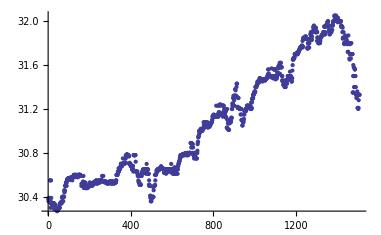

```mathematica
ListPlot[content[[2;;-1,2]]]
```

```mathematica
http://money.finance.sina.com.cn/quotes_service/view/vMS_tradehistory.php?symbol=sh601633&date=2013-03-22&page=2
```

```mathematica
content =URLFetch["http://market.finance.sina.com.cn/downxls.php?date=2013-03-22&symbol=sh601633"];
```

LibraryFunction::strerr: -- Message text not found --

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed, "\r\n"].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringSplit[$Failed, "\r\n"], ": ", 2].

```mathematica
content =URLFetch["http://money.finance.sina.com.cn/quotes_service/view/vMS_tradehistory.php?symbol=sh601633&date=2013-03-22&page=2","Parameters"->{"query"->"Mathematica HTTPClient"}]
```

<!DOCTYPE html PUBLIC "-//W3C//DTD XHTML 1.0 Transitional//EN" "http://www.w3.org/TR/xhtml1/DTD/xhtml1-transitional.dtd">
<html xmlns="http://www.w3.org/1999/xhtml">
<head>
<title>长城汽车(601633)历史成交明细数据_新浪财经_新浪网 </title>
<meta name="keywords" content="长城汽车历史成交明细,601633历史成交明细,新浪财经">
<meta name="description" content="新浪财经长城汽车(601633)行情中心,为您提供长城汽车(601633)股票历史成交明细数据统计与查询,包括成交时间,成交价格,成交量,历史交易买卖盘性质.">
<meta http-equiv="Content-Type" content="text/html; charset=gb2312" />
<link rel="stylesheet" href="http://www.sinaimg.cn/cj/transactions/css/style_history.css" type="text/css" media="all" />
<link rel="stylesheet" href="http://www.sinaimg.cn/cj/transactions/css/cld.css" type="text/css" media="all" />
<script language="javascript" type="text/javascript">
var symbol = "sh601633";
var pageDate = "2013-03-22";
var timestart = '14:39:31';
var timeend = '14:49:46';
var delistQuarter = 0;var currentPage = 2;document.domain = "finance.sina.com.cn";
</script>
<script type="text/javascript" src="http://www.sinaimg.cn/cj/transactions/js/detail_history.js"></script>
<script type="text/javascript" src="/quotes_service/view/js/dateCtrl_history.js"></script>
</head>

<body>

<div class="wrap">

<!-- 新浪财经 head begin -->
<!-- 标准二级导航_财经 begin -->
<div style="padding-top:5px;padding-bottom:5px;margin:0 auto;width:950px;">
<style type="text/css">
.secondaryHeader{height:33px;overflow:hidden;background:url(http://i2.sinaimg.cn/dy/images/header/2008/standardl2nav_bg.gif) repeat-x #fff;color:#000;font-size:12px;font-weight:100;}
.secondaryHeader a,.secondaryHeader a:visited{color:#000;text-decoration:none;}
.secondaryHeader a:hover,.secondaryHeader a:active{color:#c00;text-decoration:underline;}
.sHBorder{border:1px #e3e3e3 solid;padding:0 10px 0 12px;overflow:hidden;zoom:1;}
.sHLogo{float:left;height:31px;line-height:31px;overflow:hidden;}
.sHLogo span,.sHLogo span a,.sHLogo span a:link,.sHLogo span a:visited,.sHLogo span a:hover{display:block;*float:left;display:table-cell;vertical-align:middle;*display:block;*font-size:27px;*font-family:Arial;height:31px;}
.sHLogo span,.sHLogo span a img,.sHLogo span a:link img,.sHLogo span a:visited img,.sHLogo span a:hover img{vertical-align:middle;border:0;}
.sHLinks{float:right;line-height:31px;}
</style>
<div class="secondaryHeader">
	<div class="sHBorder">
		<div class="sHLogo"><span><a href="http://www.sina.com.cn/"><img src="http://i1.sinaimg.cn/dy/images/header/2009/standardl2nav_sina_new.gif" alt="新浪网" /></a><a href="http://finance.sina.com.cn/stock/"><img src="http://i1.sinaimg.cn/dy/images/header/2009/standardl2nav_fin_gupiao.gif" alt="新浪财经-股票" /></a></span></div>

		<div class="sHLinks"><a href="http://finance.sina.com.cn/">财经首页</a>&nbsp;|&nbsp;<a href="http://www.sina.com.cn/">新浪首页</a>&nbsp;|&nbsp;<a href="http://news.sina.com.cn/guide/">新浪导航</a></div>
	</div>
</div>
</div>
<!-- 标准二级导航_财经 end -->
<div class="navRow" id="nav"></div>
<!-- 新浪财经 head end -->


<div class="tabsOuter">
	<ul>
		<li><span><a href="vMS_tradedetail.php?symbol=sh601633">当日成交明细</a></span></li>
		<li class="active"><span>历史成交明细</span></li>
		<li><span><a href="http://vip.stock.finance.sina.com.cn/quotes_service/view/cn_price.php?symbol=sh601633">分价表</a></span></li>
		<li><span><a href="http://vip.stock.finance.sina.com.cn/quotes_service/view/cn_price_history.php?symbol=sh601633">历史分价表</a></span></li>
		<li><span><a href="http://vip.stock.finance.sina.com.cn/quotes_service/view/cn_bill.php?symbol=sh601633">大单明细</a></span></li>
	</ul>
	<div class="suggestOuter">
	<form style="position:relative;z-index:50000;" class="bar right" action="http://biz.finance.sina.com.cn/suggest/lookup_n.php" method="get" target="_self">
		<input type="hidden" name="country" value="cntrans_his" />
		<input type="text" id="inputSymbol" name="q" />
		<input type="submit" value="查看" /><a href="http://comment4.news.sina.com.cn/comment/skin/feedback.html?channel=ly&newsid=205" style="padding-right:8px;" target="_blank">意见反馈</a>
	</form>
	</div>
	<script type="text/javascript" src="http://finance.sina.com.cn/basejs/suggestServer.js"></script>
	<script type="text/javascript">
		var suggestServer = new SuggestServer();
		suggestServer.bind({
			// 除"input"必须设置外 其他均为可选
			"input": "inputSymbol", //*(必选) 指定suggest绑定的对象 [string|HTMLElement.input]
			"loader": "script_loader", // 可指定js读取用的公共容器 [string|HTMLElement]
			"default": "股票代码", // 可指定input默认值 [string] 默认空
			"type": "111", // 类型 [string] 例如"stock"、"23"、"11,12"
			/*
				type值详解
				为空时即全选
				"stock": "11,12,13,14,15"
				"fund": "21,22,23,24,25,26"
				"hkstock": "31"
				"hk": "31,32"
				"usstock": "41"
				"us": "41,42"
				[
					"111": "仅AB股"
					"11": "A 股", "12": "B 股", "13": "权证", "14": "期货", "15": "债券",
					"21": "开基", "22": "ETF", "23": "LOF", "24": "货基", "25": "QDII", "26": "封基",
					"31": "港股", "32": "窝轮",
					"41": "美股", "42": "外期"
				]
			*/
			"max": 10, // 备选项个数，<=10 [number] 默认 10
			"width": 210, // 指定宽度 [number] 默认220
			"link": "/quotes_service/view/vMS_tradehistory.php?symbol=@3@", // 备选项点击的url 不设置则不可点击 [string]
			"head": ["选项", "代码", "中文名称"], // 表头 为null时无表头 [object.array|null] 默认["选项", "代码", "名称"]
			"body": [-1, 2, 4], // 表格内容列 {-1: 选项, -2: 类型, 0: 无染色选项, 1: 类型代码详见type, 2: 代码, 3: 全称, 4: 中文名称, 5:拼音} [object.array|null] 默认[-1, 2, 4]
			"callback": null // 选定提示行时的回调方法，回调该方法时传入当前input内value [function|null]
		});
	</script>
</div>
<div class="dataOuter">
	<div class="hqRow">
		<div class="marketData" id="quote_area">
			<div>
			<span class="title"><h1><a href="http://biz.finance.sina.com.cn/suggest/lookup_n.php?country=stock&q=sh601633" target="_blank">长城汽车</a></h1>上海·sh601633</span>
			</div>
			<div class="dateWrap" id="cOuter">
				<ol id="ymdOl">
					<li class="yearLi" id="yearLi">
						<div>
							<a href="javascript:void(0);" hidefocus="true" class="up"></a>
							<dl id="yearDl"></dl>
							<a href="javascript:void(0);" hidefocus="true" class="down"></a>
						</div>
						<span><span id="yearDisplay" class="nDisplay">2013</span>年</span>
					</li>
					<li class="monthLi" id="monthLi">
						<div>
							<a href="javascript:void(0);" hidefocus="true" class="up"></a>
							<dl id="monthDl"></dl>
							<a href="javascript:void(0);" hidefocus="true" class="down"></a>
						</div>
						<span><span id="monthDisplay" class="nDisplay">03</span>月</span>
					</li>
					<li class="dayLi" id="dayLi">
						<div>
							<a href="javascript:void(0);" hidefocus="true" class="up"></a>
							<dl id="dayDl"></dl>
							<a href="javascript:void(0);" hidefocus="true" class="down"></a>
						</div>
						<span><span id="dayDisplay" class="nDisplay">22</span>日</span>
					</li>
				</ol>
				<div id="cTip">提示：鼠标<u>滚轮</u>可选择日期</div>
				<div id="cAlert">点击确认查看该日股票历史交易</div>
				<div id="cBtn"><input type="button" value="确认" id="cConfirm" /><input type="button" value="取消" id="cReset" /></div>
			</div>

			<div>
			<table>
			<tbody>
				<tr><td>收盘价:<h5><span style="color:#008000">32.81</span></h5></td><td>涨跌幅:<h6><span style="color:#008000">-2.06%</span></h6></td></tr>
				<tr><td>前收价:33.50</td><td>开盘价:33.30</td></tr>
				<tr><td>最高价:33.30</td><td>最低价:32.59</td></tr>
				<tr><td>成交量(手):26385.04</td><td>成交额(千元):86930.63</td></tr>
			</tbody>
			</table>
			</div>
		</div>

		<div class="imgWrap"><a href="http://biz.finance.sina.com.cn/suggest/lookup_n.php?country=stock&q=sh601633" target="_blank"><img src="http://market.finance.sina.com.cn/his_min/2013/03/22/sh601633.gif"alt="代码有误或没有交易数据" border="0" /></a></div>
	</div>
	<div class="main">
<div style="display: none;" id="ScriptLoader"></div>
<div class="timeline" id="ruler"></div>
</div>
<table class="datatbl" id="datatbl">
	<thead>
		<tr>
			<th style="width:14%;">成交时间</th>
			<td style="width:12%;">成交价</td>
			<td style="width:14%;">涨跌幅</td>
			<td style="width:17%;">价格变动</td>
			<td style="width:14%;">成交量(手)</td>
			<td style="width:15%;">成交额(元)</td>
			<th style="width:14%;">性质</th>
		
		</tr>
	</thead>
	<tbody>
<tr class="medium"><th>14:49:46</th><td>33.05</td><td>-1.34%</td><td>-0.01</td><td>56</td><td>185,080</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:49:36</th><td>33.06</td><td>-1.31%</td><td>+0.01</td><td>27</td><td>89,262</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:49:31</th><td>33.05</td><td>-1.34%</td><td>--</td><td>2</td><td>6,610</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:49:21</th><td>33.05</td><td>-1.34%</td><td>--</td><td>14</td><td>46,270</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:49:11</th><td>33.05</td><td>-1.34%</td><td>--</td><td>3</td><td>9,915</td><th><h6>卖盘</h6></th></tr>
<tr class="medium"><th>14:49:06</th><td>33.05</td><td>-1.34%</td><td>--</td><td>142</td><td>469,310</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:48:31</th><td>33.05</td><td>-1.34%</td><td>--</td><td>2</td><td>6,610</td><th><h5>买盘</h5></th></tr>
<tr class="medium"><th>14:48:26</th><td>33.05</td><td>-1.34%</td><td>-0.01</td><td>53</td><td>175,165</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:48:16</th><td>33.06</td><td>-1.31%</td><td>+0.01</td><td>5</td><td>16,530</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:48:06</th><td>33.05</td><td>-1.34%</td><td>-0.01</td><td>1</td><td>3,305</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:48:06</th><td>33.06</td><td>-1.31%</td><td>--</td><td>2</td><td>6,612</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:47:51</th><td>33.06</td><td>-1.31%</td><td>+0.01</td><td>15</td><td>49,590</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:47:41</th><td>33.05</td><td>-1.34%</td><td>-0.01</td><td>20</td><td>66,100</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:47:26</th><td>33.06</td><td>-1.31%</td><td>+0.01</td><td>2</td><td>6,612</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:47:11</th><td>33.05</td><td>-1.34%</td><td>+0.02</td><td>7</td><td>23,135</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:47:01</th><td>33.03</td><td>-1.40%</td><td>+0.01</td><td>8</td><td>26,424</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:46:26</th><td>33.02</td><td>-1.43%</td><td>--</td><td>1</td><td>3,302</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:46:16</th><td>33.02</td><td>-1.43%</td><td>-0.04</td><td>2</td><td>6,604</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:46:06</th><td>33.06</td><td>-1.31%</td><td>+0.04</td><td>3</td><td>9,918</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:45:56</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>12</td><td>39,624</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:45:51</th><td>33.07</td><td>-1.28%</td><td>+0.04</td><td>5</td><td>16,535</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:45:36</th><td>33.03</td><td>-1.40%</td><td>-0.04</td><td>5</td><td>16,515</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:45:31</th><td>33.07</td><td>-1.28%</td><td>+0.04</td><td>1</td><td>3,307</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:45:21</th><td>33.03</td><td>-1.40%</td><td>+0.01</td><td>2</td><td>6,606</td><th><h1>中性盘</h1></th></tr>
<tr ><th>14:44:56</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>3</td><td>9,906</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:44:51</th><td>33.07</td><td>-1.28%</td><td>--</td><td>29</td><td>95,903</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:44:36</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>11</td><td>36,377</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:44:31</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>1</td><td>3,302</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:44:26</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>1</td><td>3,307</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:44:21</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>20</td><td>66,040</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:44:11</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>1</td><td>3,307</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:44:01</th><td>33.02</td><td>-1.43%</td><td>--</td><td>1</td><td>5,250</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:43:51</th><td>33.02</td><td>-1.43%</td><td>--</td><td>2</td><td>6,604</td><th><h5>买盘</h5></th></tr>
<tr class="medium"><th>14:43:36</th><td>33.02</td><td>-1.43%</td><td>--</td><td>74</td><td>245,702</td><th><h6>卖盘</h6></th></tr>
<tr class="medium"><th>14:43:36</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>45</td><td>150,538</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:43:31</th><td>33.07</td><td>-1.28%</td><td>--</td><td>9</td><td>29,763</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:43:11</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>2</td><td>6,614</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:43:06</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>13</td><td>42,926</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:42:51</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>5</td><td>16,535</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:42:46</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>2</td><td>6,604</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:42:41</th><td>33.07</td><td>-1.28%</td><td>--</td><td>11</td><td>36,377</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:42:31</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>15</td><td>49,605</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:42:01</th><td>33.02</td><td>-1.43%</td><td>--</td><td>6</td><td>19,812</td><th><h6>卖盘</h6></th></tr>
<tr class="medium"><th>14:41:51</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>41</td><td>135,382</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:41:46</th><td>33.07</td><td>-1.28%</td><td>--</td><td>1</td><td>3,307</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:41:36</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>1</td><td>3,307</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:41:11</th><td>33.02</td><td>-1.43%</td><td>+0.01</td><td>14</td><td>46,228</td><th><h1>中性盘</h1></th></tr>
<tr ><th>14:40:56</th><td>33.01</td><td>-1.46%</td><td>-0.06</td><td>6</td><td>19,806</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:40:46</th><td>33.07</td><td>-1.28%</td><td>+0.05</td><td>15</td><td>49,605</td><th><h5>买盘</h5></th></tr>
<tr class="medium"><th>14:40:36</th><td>33.02</td><td>-1.43%</td><td>--</td><td>95</td><td>313,690</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:40:26</th><td>33.02</td><td>-1.43%</td><td>--</td><td>23</td><td>75,946</td><th><h6>卖盘</h6></th></tr>
<tr class="medium"><th>14:40:16</th><td>33.02</td><td>-1.43%</td><td>-0.05</td><td>51</td><td>168,402</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:40:16</th><td>33.07</td><td>-1.28%</td><td>--</td><td>7</td><td>23,149</td><th><h5>买盘</h5></th></tr>
<tr class="medium"><th>14:40:11</th><td>33.07</td><td>-1.28%</td><td>-0.02</td><td>61</td><td>201,727</td><th><h6>卖盘</h6></th></tr>
<tr class="medium"><th>14:40:06</th><td>33.09</td><td>-1.22%</td><td>-0.01</td><td>34</td><td>112,506</td><th><h6>卖盘</h6></th></tr>
<tr ><th>14:39:56</th><td>33.10</td><td>-1.19%</td><td>--</td><td>13</td><td>43,030</td><th><h5>买盘</h5></th></tr>
<tr ><th>14:39:31</th><td>33.10</td><td>-1.19%</td><td>--</td><td>14</td><td>46,340</td><th><h1>中性盘</h1></th></tr>
	</tbody>
</table>
<div style="height:40px;line-height:40px;text-align:right;padding-right:10px;"><a href="http://market.finance.sina.com.cn/downxls.php?date=2013-03-22&symbol=sh601633" target="_blank">明细下载</a></div>
</div>
	</div>


</div>

<style type="text/css">
#footer{width:950px; text-align:center; line-height:21px; font-size:12px;margin-top:20px;color:#333;margin-left:auto;margin-right:auto;}
</style>
<!-- SUDA_CODE_START --> 
<script type="text/javascript" src="http://www.sinaimg.cn/unipro/pub/suda_s_v851c.js"></script> 
<script type="text/javascript" > 
_S_pSt(_S_PID_); 
</script> 
<noScript> 
<div style='position:absolute;top:0;left:0;width:0;height:0;visibility:hidden'><img width=0 height=0 src='http://beacon.sina.com.cn/a.gif?noScript' border='0' alt='' /></div> 
</noScript> 
<!-- SUDA_CODE_END --> 

<!-- Start  Wrating  -->
<script language="javascript">
var wrUrl="//sina.wrating.com/";var wrDomain="sina.com.cn";var wratingDefaultAcc="860010-0323010000";var wratingAccArray={"torch.2008.sina.com.cn":"860010-0308070000","video.sina.com.cn":"860010-0309010000","cctv.sina.com.cn":"860010-0309020000","chat.sina.com.cn":"860010-0311010000","ent.sina.com.cn":"860010-0312010000","tech.sina.com.cn":"860010-0313010000","mobile.sina.com.cn":"860010-0313020000","house.sina.com.cn":"860010-0315010000","bj.house.sina.com.cn":"860010-0315020000","auto.sina.com.cn":"860010-0316010000","eladies.sina.com.cn":"860010-0317010000","bj.sina.com.cn":"860010-0317020000","woman.sina.com.cn":"860010-0317010000","women.sina.com.cn":"860010-0317010000","lady.sina.com.cn":"860010-0317010000","man.eladies.sina.com.cn":"860010-0317030000","games.sina.com.cn":"860010-0318010000","game.sina.com.cn":"860010-0318010000","edu.sina.com.cn":"860010-0307010000","baby.sina.com.cn":"860010-0320010000","kid.sina.com.cn":"860010-0320020000","astro.sina.com.cn":"860010-0321020000","news.sina.com.cn":"860010-0310010000","weather.news.sina.com.cn":"860010-0310020000","mil.news.sina.com.cn":"860010-0310030000","www.sina.com.cn":"860010-0322010000","home.sina.com.cn":"860010-0322010000","sports.sina.com.cn":"860010-0308010000","shidefc.sina.com.cn":"860010-0308020000","weiqi.sina.com.cn":"860010-0308030000","f1.sina.com.cn":"860010-0308040000","golf.sina.com.cn":"860010-0308050000","2002.sina.com.cn":"860010-0308060000","2004.sina.com.cn":"860010-0308060000","2006.sina.com.cn":"860010-0308060000","2008.sina.com.cn":"860010-0308070000","yayun2002.sina.com.cn":"860010-0308060000","yayun2006.sina.com.cn":"860010-0308060000","inter.sina.com.cn":"860010-0308080000","chelsea.sina.com.cn":"860010-0308090000","book.sina.com.cn":"860010-0319010000","cul.book.sina.com.cn":"860010-0319020000","comic.book.sina.com.cn":"860010-0319030000","finance.sina.com.cn":"860010-0314010000","money.sina.com.cn":"860010-0314020000","yue.sina.com.cn":"860010-0324010000","www.sina.com":"860010-0322010000"};function vjTrack(){var U=1800;var T=false;var S=false;var R="";var Q="0";var P="";var N;var L;var K;var J;var I;var H="expires=Fri, 1 Jan 2038 00:00:00 GMT;";var G=0;if(document.location.protocol=="file:"){return }T=navigator.cookieEnabled?"1":"0";S=navigator.javaEnabled()?"1":"0";var F="0";var E;var C=-1;var D=document.cookie;if(T=="1"){C=D.indexOf("vjuids=");if(C<0){E=vjVisitorID();document.cookie="vjuids="+escape(E)+";"+H+";domain="+wrDomain+";path=/;";if(document.cookie.indexOf("vjuids=")<0){T="0"}else{Q="1"}}else{E=vjGetCookie("vjuids")}}L=document.referrer;if(!L||L==""){L=""}R=vjFlash();if(self.screen){N=screen.width+"x"+screen.height+"x"+screen.colorDepth}else{if(self.java){var M=java.awt.Toolkit.getDefaultToolkit();var O=M.getScreenSize();N=O.width+"x"+O.height+"x0"}}if(navigator.language){K=navigator.language.toLowerCase()}else{if(navigator.browserLanguage){K=navigator.browserLanguage.toLowerCase()}else{K="-"}}I="";var B;var X;X=new Date();J=X.getTimezoneOffset()/-60;J=X.getTimezoneOffset()/-60;B="&s="+N+"&l="+K+"&z="+J+"&j="+S+"&f="+R;if(T=="1"){C=document.cookie.indexOf("vjlast=");if(C<0){G=0}else{G=parseInt(vjGetCookie("vjlast"))}}if((X.getTime()/1000)-G>U){F="1";document.cookie="vjlast="+Math.round(X.getTime()/1000)+";"+H+";domain="+wrDomain+";path=/;"}if(L!=""){B=B+"&r="+escape(L)}if(F!="0"){B=B+"&n="+G}if(Q!="0"){B=B+"&u="+Q}var V;var A=vjGetAcc();var W=vjGetDomain();V=wrUrl+"a.gif?a="+X.getTime().toString(16)+"&t="+escape(I)+"&i="+escape(E)+"&b="+escape(document.location)+"&c="+A+B+"&ck="+W;document.write('<img src="'+V+'" width="1" height="1" />')}function vjGetAcc(){var B=document.location.toString().toLowerCase();var C=(B.split("/"))[2];var A=wratingAccArray[C];if(typeof (A)=="undefined"){A=wratingDefaultAcc}return A}function vjFlash(){var _wr_f="-",_wr_n=navigator;if(_wr_n.plugins&&_wr_n.plugins.length){for(var ii=0;ii<_wr_n.plugins.length;ii++){if(_wr_n.plugins[ii].name.indexOf("Shockwave Flash")!=-1){_wr_f=_wr_n.plugins[ii].description.split("Shockwave Flash ")[1];break}}}else{if(window.ActiveXObject){for(var ii=10;ii>=2;ii--){try{var fl=eval("new ActiveXObject('ShockwaveFlash.ShockwaveFlash."+ii+"');");if(fl){_wr_f=ii+".0";break}}catch(e){}}}}return _wr_f}function vjHash(B){if(!B||B==""){return 0}var D=0;for(var C=B.length-1;C>=0;C--){var A=parseInt(B.charCodeAt(C));D=(D<<5)+D+A}return D}function vjVisitorID(){var B=vjHash(document.location+document.cookie+document.referrer).toString(16);var A;A=new Date();return B+"."+A.getTime().toString(16)+"."+Math.random().toString(16)}function vjGetCookieVal(B){var A=document.cookie.indexOf(";",B);if(A==-1){A=document.cookie.length}return unescape(document.cookie.substring(B,A))}function vjGetCookie(C){var B=C+"=";var F=B.length;var A=document.cookie.length;var E=0;while(E<A){var D=E+F;if(document.cookie.substring(E,D)==B){return vjGetCookieVal(D)}E=document.cookie.indexOf(" ",E)+1;if(E==0){break}}return null}function vjGetDomain(){var A=0;try{if(window.self.parent!=self){var D=/sina.com/i;var C=document.location.toString().toLowerCase();var B=parent.location.toString().toLowerCase();if(D.test(C)&&D.test(B)){A=1}}}catch(e){A=1}return A}vjTrack();
</script>
<!-- End Wrating-->
<div id="footer">
　客户服务热线：4006900000　　欢迎批评指正<br>
<a target="_blank" href="http://tech.sina.com.cn/focus/sinahelp.shtml">常见问题解答</a> 
 <a target="_blank" href="http://net.china.cn/chinese/index.htm">互联网违法和不良信息举报</a>　
 <a target="_blank" href="http://comment4.news.sina.com.cn/comment/skin/feedback.html?channel=ly&amp;newsid=5">新浪财经意见反馈留言板</a>
 <br><br><a href="http://corp.sina.com.cn/chn/">新浪简介</a> | <a href="http://corp.sina.com.cn/eng/">About Sina</a> | <a href="http://emarketing.sina.com.cn/">广告服务</a> | <a href="http://www.sina.com.cn/contactus.html">联系我们</a> | <a href="http://corp.sina.com.cn/chn/sina_job.html">招聘信息</a> | <a href="http://www.sina.com.cn/intro/lawfirm.shtml">网站律师</a> | <a href="http://english.sina.com">SINA English</a> | <a href="http://members.sina.com.cn/apply/">通行证注册</a> | <a href="http://help.sina.com.cn/">产品答疑</a><br><br>Copyright &copy; 1996-2012 SINA Corporation, All Rights Reserved<br><br>新浪公司　<a target="_blank" href="http://www.sina.com.cn/intro/copyright.shtml">版权所有</a>
</div>



</body>

<script type="text/javascript">
<!--//--><![CDATA[//><!--
function checkiask(){
	if (document._searchiask.k.value=="请输关键词" || document._searchiask.k.value=="" ){
		//window.open("http://iask.com");
		document._searchiask.k.value = "请输关键词";
		document._searchiask.k.className = "iaskRedTxt";
		document._searchiask.k.style.border = "1px #f00 solid";
		return false;
	}
	return true;
}
function sens(){//搜新闻
	document._searchiask.t.value = "keyword";
}
function sezt(){//搜专题
	document._searchiask.t.value = "subject";
}
//--><!]]>
</script>
	
<!--google begin-->
<!-- Script Used for Clickable Google Logo, and Google Text Link -->
<script type="text/javascript">
function submitFormWithChannel(channelname){
	if(document.gform.q.value=="请输关键词"||document.gform.q.value=="请输入关键字"||document.gform.q.value==""){
		document.gform.q.value="请输关键词";
	}else{
		document.gform.channel.value=channelname;
		document.gform.submit();
		return;
	}
}
</script>
<!-- End of Script for Clickable Google Logo -->

<script type="text/javascript">
function checkGoogleValue(){
	if(document.gform.q.value=="请输关键词"||document.gform.q.value=="请输入关键字"||document.gform.q.value==""){
		document.gform.q.value="请输关键词";
		return false;
	}
	document.gform.channel.value = "osearch";
	return true;
}
</script>

<script type="text/javascript">
function hidealla(j){
	for(j=1;j<3;j++){
		document.getElementById("surveya"+j).style.visibility = "hidden";
	}
}
function showdiv1(h){
	hidealla();
	document.getElementById("surveya"+h).style.visibility = "visible";
}
</script>

<script type="text/javascript">
//<![CDATA[
if (!window.frames["list_frame"] ) {
	main();
}
DateCtrl.initYear=2011;
DateCtrl.endYear=2013;
DateCtrl.Init();
generateNav();
//alert(window.frames["list_frame"].document.getElementById("datatbl").tagName);
//]]>
</script>

</html>